```mathematica
myFontStandard=fontStandard="Calibri";
myFontSize=fontSize=13;
colors=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/myCMYKcolors.m"][[1]]
colorlist=Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/myCMYKcolors.m"][[2]]
mycolor="Türkis"/.colorlist
myTickStyle=TicksStyle->Directive[FontFamily->fontStandard];
myStyleFunction[l_List]:=Module[{},Style[#,FontFamily->fontStandard,FontSize->fontSize]&/@l]
myStyle[s_String]:=Module[{},Style[s,FontFamily->fontStandard,FontSize->fontSize,Black]]

myGray=CMYKColor[0,0,0,.15]

colors=Insert[Delete[colors,1],CMYKColor[0,.10,1.00,0.07],1]
colors=Insert[Delete[colors,6],CMYKColor[0,0,1,0],6]

Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/myPackage.wl"];
myPackageInputPrint[]
(*Rapsgelb-Graphics-*)
```

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]}

CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]

CMYKColor[0, 0, 0, 0.15]

{CMYKColor[0, 0.1, 1., 0.07],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{CMYKColor[0, 0.1, 1., 0.07],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0, 1, 0],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

SetDelayed::write: Tag Rule in (TicksStyle→Directive[FontFamily→Calibri])[fontsize_Integer:13,fontfamily_String:Calibri,color_:color] is Protected.

Definition::ssym: color is not a symbol.

Definition::ssym: TicksStyle→Directive[FontFamily→Calibri] is not a symbol.

General::stop: Further output of Definition::ssym will be suppressed during this calculation.

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]

myExportF[l_List]:=Module[{r,g,name},((r=600;g=#1⟦1⟧;name=#1⟦2⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}];r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Calibri,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Calibri,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]

myLabelStyle[fontsize_Integer:13,fontfamily_String:Calibri,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Calibri,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotStyle[opacity_:1]:=Module[{},(PlotStyle→Directive[Opacity[opacity],#1]&)/@myPlotColors]
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_String]:=Module[{},Style[s,FontFamily→fontStandard,FontSize→fontSize,Black]]
 
myStyle[s_,fontsize_Integer:13,fontfamily_String:Calibri,color_:GrayLevel[0]]:=Module[{},Style[ToString[s],FontSize→fontsize,FontFamily→fontfamily,color]]
myStyleFunction[l_List]:=Module[{},(#1&)/@l]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]

myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

```mathematica
(*exPath="C:\\Users\\mona_\\OneDrive\\Jummeds\\Arbeitsgruppen\\Arbeitsmedizin\\Lärmschwerhörigkeit MusikerInnen Literaturübersicht\\Publikation\\Abbildungen\\";
*)exPath=NotebookDirectory[]~~"output\\";

exportF[l_List]:=Module[{r,g,name},

Map[
(r=600;g=#[[1]];name=#[[2]];
(*Export für Druck im CMYK-Farbraum 600 dpi als Standard*)
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi CMYK"~~i,ColorConvert[Rasterize[g,ImageResolution->r],"CMYK"]],{i,{".eps",".png"}}];

(*Export für Web-Graphik mit Wunsch-dpi *)
r=#[[3]];
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi"~~i,Rasterize[g,ImageResolution->r]],{i,{".png"}}];

(*Export als Vektorgraphic*)
Table[Export[exPath~~name~~i,g],{i,{".svg"}}]&/@#
)&,l
]
]

exportFSVG[l_List]:=Module[{r,g,name},

Map[
(g=#[[1]];name=#[[2]];
(*Export als Vektorgraphic*)
Table[Export[exPath~~name~~i,g],{i,{".svg"}}]&/@#
)&,l
]
]

exportFPNG[l_List]:=Module[{r,g,name},

Map[
((*Export für Web-Graphik mit Wunsch-dpi *)
g=#[[1]];name=#[[2]];
r=#[[3]];
Table[Export[exPath~~name~~" "~~ToString@r~~" dpi"~~i,Rasterize[g,ImageResolution->r]],{i,{".png"}}]
)&,l
]
]
```

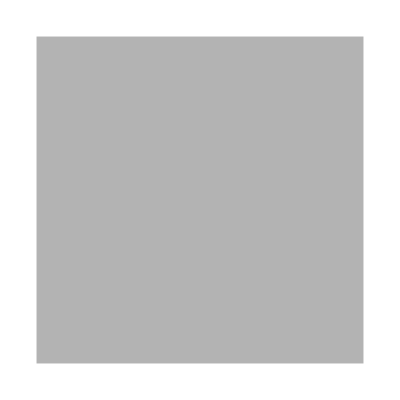
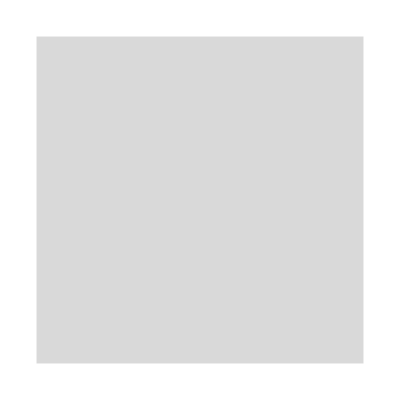

```mathematica
myGray=CMYKColor[0,0,0,.15];
Graphics[{#,Rectangle[]}]&/@{CMYKColor[0,0,0,.3],myGray}
```

```mathematica
d = Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/Extract%20from%20Full%20Text%20Analysis.xlsx"][[1]];

nClassic=Select[d,StringContainsQ[#[[2]],"Classic"]&];
nTrad=Select[d,StringContainsQ[#[[2]],"Traditional"]||StringContainsQ[#[[2]],"Dance"]&];
nRPJ=Select[d,StringContainsQ[#[[2]],"Rock"]||StringContainsQ[#[[2]],"Pop"]||StringContainsQ[#[[2]],"Jazz"]&];
nMil=Select[d,StringContainsQ[#[[2]],"Military"]||StringContainsQ[#[[2]],"Marching"]&];

nNA=Select[d,StringContainsQ[#[[2]],"?"]||StringContainsQ[#[[2]],"Unknown"]||StringContainsQ[#[[2]],"Mixed"]&];
groups={nClassic,nRPJ,nTrad,nMil,nNA};
colorForGroups={"Classical Music"->CMYKColor[0, 0.1, 1., 0.07],"Rock, Pop, Jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"Traditional Music, Dance Music"->CMYKColor[{0, Rational[3, 5], 1, 0}],"Military Music, Marching Band Music"->CMYKColor[{1, Rational[11, 20], 0, 0}],"Unknown, Mixed Genre"->CMYKColor[{0, Rational[9, 10], 1, 0}]};
colorForGroupsLC={"classical music"->CMYKColor[0, 0.1, 1., 0.07],"rock, pop, jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"traditional music, dance music"->CMYKColor[{0, Rational[3, 5], 1, 0}],"military music, marching band music"->CMYKColor[{1, Rational[11, 20], 0, 0}],"unknown, mixed genre"->CMYKColor[{0, Rational[9, 10], 1, 0}]};
colorForGroupsDE={"klassische Musik"->CMYKColor[0, 0.1, 1., 0.07],"Rock, Pop, Jazz"->CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],"unbekanntes, gemischtes Genre"->CMYKColor[{0, Rational[9, 10], 1, 0}],"traditionelle Musik, Tanzmusik"->CMYKColor[{0, Rational[3, 5], 1, 0}],"Militärmusik, Marschmusik"->CMYKColor[{1, Rational[11, 20], 0, 0}]};
```

```mathematica
toGerman={"Classic"->"klassische Musik","Rock, Pop, Jazz"->"Rock, Pop, Jazz","Traditional Music, Dance Music"->"traditionelle Musik, Tanzmusik","Military Music, Marching Band Music"->"Militärmusik, Marschmusik","Classical Music"->"klassische Musik","Traditional"->"traditionelle Musik","Unknown"->"unbekanntes Genre","Mixed"->"gemischte Genre","Dance"->"Tanzmusik","Military Music"->"Militärmusik","Marching Band"->"Marschmusik"}
```

{Classic→klassische Musik,Rock, Pop, Jazz→Rock, Pop, Jazz,Traditional Music, Dance Music→traditionelle Musik, Tanzmusik,Military Music, Marching Band Music→Militärmusik, Marschmusik,Classical Music→klassische Musik,Traditional→traditionelle Musik,Unknown→unbekanntes Genre,Mixed→gemischte Genre,Dance→Tanzmusik,Military Music→Militärmusik,Marching Band→Marschmusik}

## Pie Chart

```mathematica
groupsPiechart=ReverseSort[Association@(#[[2]]->#[[1]]&/@Transpose[{Length/@groups,ToLowerCase/@{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance Music","Military Music, Marching Band Music","Unknown, Mixed Genre"}}])];

chartPieChartGroups=PieChart[groupsPiechart,ChartLabels->Values[groupsPiechart],ImageSize->{600,600},ChartStyle->(Keys[groupsPiechart]/. colorForGroupsLC),LabelStyle->Directive[ FontSize->40,FontFamily->fontStandard],LegendAppearance->{LegendMarkerSize->50,FontFamily->fontStandard},ChartLegends->Keys[groupsPiechart]]
```

-Graphics-

```mathematica
groupsPiechart=ReverseSort[Association@(#[[2]]->#[[1]]&/@Transpose[{Length/@groups,{"klassische Musik","Rock, Pop, Jazz","traditionelle Musik, Tanzmusik","Militärmusik, Marschmusik","unbekanntes, gemischtes Genre"}}])];

chartPieChartGroupsDE=PieChart[groupsPiechart,ChartLabels->Values[groupsPiechart],ImageSize->{600,600},ChartStyle->(Keys[groupsPiechart]/. colorForGroupsDE),LabelStyle->Directive[ FontSize->40,FontFamily->fontStandard],LegendAppearance->{LegendMarkerSize->50,FontFamily->fontStandard},ChartLegends->Keys[groupsPiechart]]
```

-Graphics-

```mathematica
StringSplit[#,", "]&/@Rest[d[[All,2]]];
If[StringContainsQ[#,"?"][[1]]==True,{"Unknown"},#]&/@%;
labelPieChart=ReverseSortBy[Tally@Flatten@%,#[[2]]&]/. {"Classic"->"Classical Music","Dance"->"Dance Music","Traditional"->"Traditional Music","Marching Band"->"Marching Band Music"};

#[[1]]~~ " n="~~ToString[#[[2]]]->#[[2]]&/@%;
Association[%];
chartPieChart=PieChart[%,ChartLabels->Callout[labelPieChart[[All,2]]],ImageSize->{600,600},LabelStyle->Directive[ FontSize->30,FontFamily->fontStandard],ChartStyle->Delete[colors,10],ChartLegends->ToLowerCase/@labelPieChart[[All,1]],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}]
```

-Graphics-

```mathematica
StringSplit[#,", "]&/@Rest[d[[All,2]]];
If[StringContainsQ[#,"?"][[1]]==True,{"Unknown"},#]&/@%;
labelPieChart=ReverseSortBy[Tally@Flatten@%,#[[2]]&];

#[[1]]~~ " n="~~ToString[#[[2]]]->#[[2]]&/@%;
Association[%];
chartPieChartDE=PieChart[%,ChartLabels->Callout[labelPieChart[[All,2]]],ImageSize->{600,600},LabelStyle->Directive[ FontSize->30,FontFamily->fontStandard],ChartStyle->Delete[colors,10],ChartLegends->labelPieChart[[All,1]],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}]/.toGerman
```

-Graphics-

```mathematica
exportF[{{chartPieChartDE,"Tortendiagramm",600},{chartPieChartGroupsDE,"Tortendiagramm Gruppen",600},{chartPieChart,"Pie Chart",600},{chartPieChartGroups,"Pie Chart Groups",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg},{C:\Users\mona_\Desktop\Ausgabe\Tortendiagramm Gruppen.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg},{C:\Users\mona_\Desktop\Ausgabe\Pie Chart Groups.svg}}}

## Histogram n

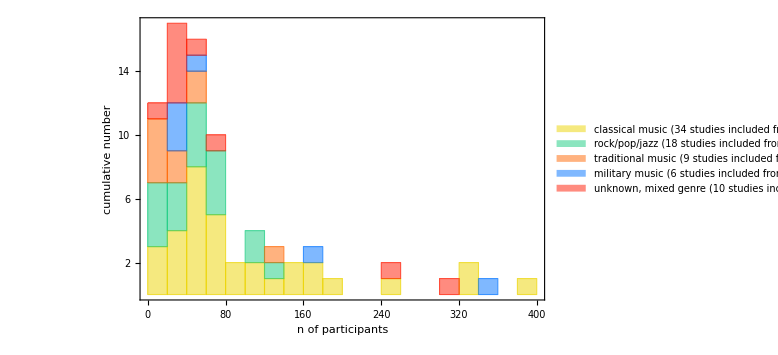

```mathematica
nPart=.
histogNpartGroups[l_List]:=Module[{n,temp},temp=(StringSplit[#,"\n"][[1]]&/@#)&/@l;
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n=Map[{#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&,temp,{2}];
nPart=n;
Histogram[ToExpression/@n[[All,All,1]],
25,
ChartLayout->"Stacked",
ChartLegends->ToLowerCase/@{"Classical Music"~~"\n("~~ToString[Length@n[[1]]] ~~" studies included from "~~ ToString[Length@l[[1]]]~~")", "Rock/Pop/Jazz"~~"\n("~~ToString[Length@n[[2]]] ~~" studies included from "~~ ToString[Length@l[[2]]]~~")","Traditional Music"~~"\n("~~ToString[Length@n[[3]]] ~~" studies included from "~~ ToString[Length@l[[3]]]~~")","Military Music"~~"\n("~~ToString[Length@n[[4]]] ~~" studies included from "~~ ToString[Length@l[[4]]]~~")","Unknown, mixed Genre"~~"\n("~~ToString[Length@n[[5]]] ~~" studies included from "~~ ToString[Length@l[[5]]]~~")"},

ImageSize->Large,
ChartStyle->colors,
myTickStyle,

Frame->True,
FrameLabel->{"n of participants","cumulative number"},
FrameTicks->{Range[2,18,2],{Range[0,410,40],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18],
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22],

LabelStyle->Directive[ FontSize->20,FontFamily->fontStandard,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]
]



charthistoNGroups=histogNpartGroups[groups[[All,All,4]]]
```

```mathematica
Export[exPath~~"IQR number of participants all data.txt",Quartiles[Flatten[ToExpression/@nPart[[All,All,1]]]]//N]
Quartiles[Flatten[ToExpression/@nPart[[All,All,1]]]]//N

nPartIQ=Sort/@ToExpression/@nPart[[All,All,1]];
maxNList=Length/@nPartIQ;
nPartIQ=SplitBy[#,#>=31|#>=56|#>=111&]&/@nPartIQ;
nPartIQ=Map[Which[Last[#]<=31,31->#,Last[#]<=56,56->#,Last[#]<=111,111->#,Last[#]>=111,112->#,True,{Null}]&,nPartIQ,{2}];
nPartIQ[[All,All,2]]=Map[Length[#]&,nPartIQ[[All,All,2]],{2}];
nPartIQ[[All,All,2]]=nPartIQ[[All,All,2]]/maxNList;
nPartIQ=
{31,56,111,112}/.Join[#,{31->0,56->0,111->0,112->0}]&/@nPartIQ;
nPartIQ=N[nPartIQ*100,3];
nPartIQ=Transpose/@Transpose[{nPartIQ*maxNList/100,nPartIQ}]; (*n and %*)
Total/@nPartIQ;
nPartIQ=Style[TableForm[nPartIQ,TableHeadings->{{"Classical Music n\n%","Rock, Pop, Jazz n\n%","Traditional Music, Dance n\n%","Military Music, Marching Band Music n\n%","Unknown Genre n\n%"},{"1. Quartile","2. Quartile","3. Quartile","4. Quartile"}}],FontFamily->fontStandard,FontSize->fontSize]
Export[exPath~~"Quartiles Study Participants Categories.pdf",nPartIQ]
```

C:\Users\mona_\Desktop\Ausgabe\IQR number of participants all data.txt

{29.75,50.,109.5}

| 1. Quartile | 2. Quartile | 3. Quartile | 4. Quartile
Classical Music n
% | 5.
14.7 | 7.
20.6 | 11.
32.4 | 11.
32.4
Rock, Pop, Jazz n
% | 7.
38.9 | 4.
22.2 | 4.
22.2 | 3.
16.7
Traditional Music, Dance n
% | 5.
55.6 | 3.
33.3 | 0
0 | 1.
11.1
Military Music, Marching Band Music n
% | 1.
16.7 | 3.
50. | 0
0 | 2.
33.3
Unknown Genre n
% | 2.
20. | 5.
50. | 1.
10. | 2.
20.

C:\Users\mona_\Desktop\Ausgabe\Quartiles Study Participants Categories.pdf

```mathematica
nPartIQ=Sort/@ToExpression/@nPart[[All,All,1]];
maxNList=Length/@nPartIQ;
nPartIQ=SplitBy[#,#>=40|#>=80|#>=100|#>=200|#>=300&]&/@nPartIQ;
nPartIQ=Map[Which[Last[#]<=40,40->#,Last[#]<=80,80->#,Last[#]<=100,100->#,Last[#]<=200,200->#,Last[#]<=300,300->#,Last[#]>=300,301->#,True,{Null}]&,nPartIQ,{2}];
nPartIQ[[All,All,2]]=Map[Length[#]&,nPartIQ[[All,All,2]],{2}];
nPartIQ[[All,All,2]]=nPartIQ[[All,All,2]]/maxNList;
nPartIQ=
{40,80,100,200,300,301}/.Join[#,{40->0,80->0,100->0,200->0,300->0,301->0}]&/@nPartIQ;
nPartIQ=N[nPartIQ*100,3];
Total/@nPartIQ;
nPartIQ=Style[TableForm[nPartIQ,TableHeadings->{{"Classical Music","Rock, Pop, Jazz","Traditional Music, Dance","Military Music, Marching Band Music","Unknown Genre"},{"<40","<80","<100","<200","<300",">300"}}],FontFamily->fontStandard,FontSize->fontSize]
Export[exPath~~"Distribution Percent Study Participants Categories.pdf",nPartIQ]
```

| <40 | <80 | <100 | <200 | <300 | >300
Classical Music | 20.6 | 38.2 | 5.88 | 23.5 | 2.94 | 8.82
Rock, Pop, Jazz | 38.9 | 44.4 | 0 | 16.7 | 0 | 0
Traditional Music, Dance | 66.7 | 22.2 | 0 | 11.1 | 0 | 0
Military Music, Marching Band Music | 50. | 16.7 | 0 | 16.7 | 0 | 16.7
Unknown Genre | 60. | 20. | 0 | 0 | 10. | 10.

C:\Users\mona_\Desktop\Ausgabe\Distribution Percent Study Participants Categories.pdf

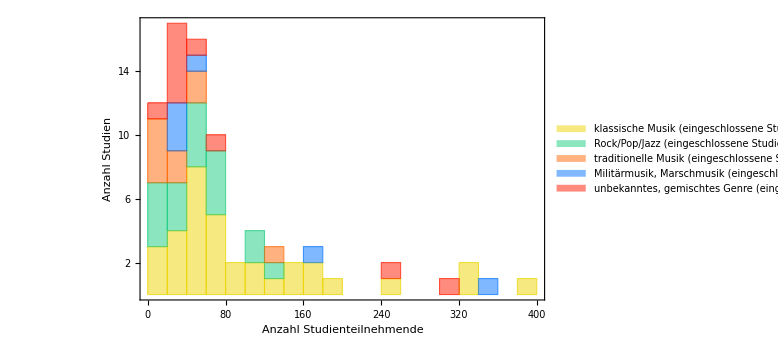

```mathematica
histogNpartGroupsDE[l_List]:=Module[{n,temp},temp=(StringSplit[#,"\n"][[1]]&/@#)&/@l;
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n=Map[{#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&,temp,{2}];
Histogram[ToExpression/@n[[All,All,1]],25,FrameTicks->{Range[2,18,2],{Range[0,410,40],Automatic}},ImageSize->Large,ChartLegends->{"klassische Musik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[1]]] " von "<> ToString[Length@l[[1]]]<>")", "Rock/Pop/Jazz"<>"\n (eingeschlossene Studien: " <>ToString[Length@n[[2]]] " von "<> ToString[Length@l[[2]]]<>")","traditionelle Musik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[3]]]" von "<> ToString[Length@l[[3]]]<>")","Militärmusik, Marschmusik"<>"\n(eingeschlossene Studien: "<>ToString[Length@n[[4]]]" von "<> ToString[Length@l[[4]]]<>")","unbekanntes, gemischtes Genre"<>"\n(eingeschlossene Studien: "~~ToString[Length@n[[5]]] ~~" von "~~ ToString[Length@l[[5]]]~~")"},LabelStyle->Directive[ FontSize->20,FontFamily->fontStandard,Black],ChartLayout->"Stacked",myTickStyle,ChartStyle->colors,Frame->True,FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18],FrameLabel->{"Anzahl Studienteilnehmende","Anzahl Studien"},FrameStyle->Directive[FontFamily->fontStandard,FontSize->22],LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}]
]

charthistoNGroupsDE=histogNpartGroupsDE[groups[[All,All,4]]]
```

```mathematica
exportF[{{charthistoNGroupsDE,"Histogramm Anzahl Studienteilnehmende",600},{charthistoNGroups,"Histogram n Participants",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm Anzahl Studienteilnehmende.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram n Participants.svg}}}

## Gender analysis

```mathematica
63/2//N
```

31.5

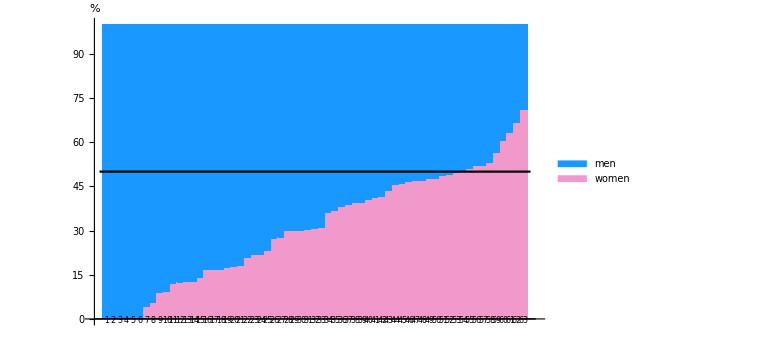
-Graphics-sex distribution as bar chart
(63 studies included from 77)1 | Audiological and electrophysiological assessment of professional pop/rock musicians    Samelli, A. G.; Matas, C. G.; Carvallo, R. M.; Gomes, R. F.; de Beija, C. S.; Magliaro, F. C.; Rabelo, C. M. (2012)
2 | Auditory thresholds among military musicians: conventional and high frequency    Gonçalves, C. G.; Lacerda, A. B.; Zeigelboim, B. S.; Marques, J. M.; Luders, D.  (2013)
3 | Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana    Setiawan, E. P.; Maryati, M. R. (2018)
4 | Noise exposure and auditory thresholds of military musicians: a follow up study    Müller, R.; Schneider, J. (2018)
5 | Temporary threshold shift in rock-and-roll musicians    Jerger, J.; Jerger, S. (1970)
6 | The influence of sound exposure onset and duration to the hearing loss prevalence in musicians    Widuri, A.; Gartiwa, G.; Pujiyanto, E. (2022)
7 | Pop-rock musicians: assessment of their satisfaction provided by hearing protectors    Santoni, C. B.; Fiorini, A. C. (2010)
8 | Valencia's cathedral church bell acoustics impact on the hearing abilities of bell ringers    García, L.; Parra, L.; Gomis, B. P.; Cavallé, L.; Pérez Guillén, V.; Pérez Garrigues, H.; Lloret, J. (2019)
9 | Sound exposure and audiometric profile of military police band musicians    Lüders, D.; Da Silva Martins, K. R. R.; De Lacerda, A. B. M.; De Oliveira Gonçalves, C. G.; Heupa, A. B. (2017)
10 | Ototraumatic effects of hard rock music    Reddell, R. C.; Lebo, C. P. (1972)
11 | Hearing in nonprofessional pop/rock musicians    Schmuziger, N.; Patscheke, J.; Probst, R. (2006)
12 | An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry    Schmuziger, N.; Patscheke, J.; Probst, R. (2007)
13 | Transient evoked otoacoustic emissions in rock musicians    Høydal, E. H.; Lein Størmer, C. C.; Laukli, E.; Stenklev, N. C. (2017)
14 | Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015)
15 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
16 | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
17 | Perception of hearing loss in orchestral musicians    Gebel, E.; Jones, S. M.; Honaker, J. A. (2017)
18 | Noise-induced hearing loss among professional musicians    Pouryaghoub, G.; Mehrdad, R.; Pourhosein, S. (2017)
19 | Study of the hearing of rock and roll musicians    Maia, J. R.; Russo, I. C. (2008)
20 | Acceptance of hearing protection aids in members of an instrumental and voice music band    Helena Mendes, M.; Catalani Morata, T; Mendes Marques, J. (2007)
21 | Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians    Halevi-Katz, D. N.; Yaakobi, E.; Putter-Katz, H. (2015)
22 | Hearing loss in steelband musicians    Juman, S.; Karmody, C. S.; Simeon, D. (2004)
23 | Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists    Hoffman, J. S.; Cunningham, D. R.; Lorenz, D. J. (2006)
24 | Sound exposures and hearing thresholds of symphony orchestra musicians    Royster, J. D.; Royster, L. H.; Killion, M. C. (1991)
25 | Hearing development in classical orchestral musicians. A follow-up study    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
26 | Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016)
27 | Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014)
28 | Effects of instrument type and orchestral position on hearing sensitivity for 0.25 to 20 kHz in the orchestral musician    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1985)
29 | Extended high frequency hearing sensitivity. A normative threshold study in musicians    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1986)
30 | Hearing assessment of classical orchestral musicians    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
31 | Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008)
32 | Acoustic trauma in classical music players    Morais, D; Benito, J. I.; Almaraz, A. (2007)
33 | Assessment of hearing and hearing disorders in rock/jazz musicians    Kähärit, K.; Zachau, G.; Eklöf, M.; Sandsjö, L.; Möller, C. (2003) | 34 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
35 | Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994)
36 | Music students: conventional hearing thresholds and at high frequencies    Lüders, D.; Gonçalves, C. G.; Lacerda, A. B.; Ribas, Â.; Conto, J. d. (2014)
37 | Auditory electrophysiological and perceptual measures in student musicians with high sound exposure    Washnik, N. J. ; Bhatt, I. S.; Sergeev, A. V.; Prabhu, P.; Suresh, C. (2023)
38 | Hearing loss in relation to sound exposure of professional symphony orchestra musicians    Schmidt, J. H.; Pedersen, E. R.; Paarup, H. M.; Christensen-Dalsgaard, J.; Andersen, T.; Poulsen, T.; Bælum, J. (2014)
39 | Hearing loss among classical-orchestra musicians    Toppila, E.; Koskinen, H.; Pyykkö, I. (2011)
40 | Hearing loss and mental health issues in amateur and professional musicians    Maghiar, M. J.;  Lawrence, B. J.; Mulders, W. H. A. M; Moyle, T. C.; Livings, I.; Jayakody, D. M. P.  (2023)
41 | Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians    Wegner, R.; Wendlandt, P.; Poschadel, B.; Olma, K.; Szadkowski, D. (2000)
42 | Review of orchestra musicians' hearing loss riskss    Eaton, S.; Gillis, H. (2002)
43 | The audiological health of horn players    Wilson, W. J.; O'Brien, I.; Bradley, A. P. (2013)
44 | Hearing ability in Danish symphony orchestra musicians    Obeling, L.; Poulsen, T. (1999)
45 | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
46 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
47 | Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras    Jansen, E. J.; Helleman, H. W.; Dreschler, W. A.; de Laat, J. A. (2009)
48 | Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds    Couth, S.; Prendergast, G.; Guest, H.; Munro, K. J.; Moore, D. R.; Plack, C. J.; Ginsborg, J.; Dawes, P. (2020)
49 | A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians    Dreyer, B.; Pottas, L.; Soer, M. E.; Graham, M. A.  (2023)
50 | Noise exposure and hearing loss in classical orchestra musicians    Russo, F. A.; Behar, A.; Chasin, M.; Mosher, S. (2013)
51 | Exposure to excessive sounds and hearing status in academic classical music students    Pawlaczyk-Łuszczyńska, M.; Zamojska-Daniszewska, M.; Dudarewicz, A.; Zaborowski, K. (2017)
52 | Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998)
53 | Hearing conservation program for marching band members: a risk for noise-induced hearing loss?    Jin, S. H.; Nelson, P. B.; Schlauch, R. S.; Carney, E. (2013)
54 | ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?    Kikidis, D.; Vardonikolaki, A.; Zachou, Z.; Razou, A.; Pantos, P.; Bibas, A. (2020)
55 | Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians    Ramma, L. (2021)
56 | Hearing loss in British Army musicians    Patil, M. L.; Sadhra, S.; Taylor, C.; Folkes, S. E. (2013)
57 | The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test    Gündüz, B.; Yıldırım Gökay, N.; Orhan, E.; Yılmaz, M. (2022)
58 | Evidence of noise-induced hearing loss among orchestral musicians    Backus, B. C.; Williamon, A. (2009)
59 | Prevalence of hearing loss among university music students    Comeau, G.; Koravand, A.; Swirp, M. (2018)
60 | Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018)
61 | Noise exposure and hearing protection in marching band students    Myers, E. (2021)
62 | Effect of musical training on masking paradigm    Devi, N.; Swathi, C. S. (2016)
63 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)

```mathematica
datagenderAnalysis=.
genderAnalysis=.
genderAnalysis[l_List]:=Module[{n,temp,ngender,genderfrac,ngenderTitles,genderfracTitles},temp=Map[{StringSplit[#[[1]],"\n"][[1]],#[[2]]}&,l,{1}];
temp=If[#[[1]]=!="-",{StringSplit[#[[1]]," "],#[[2]]},Nothing]&/@temp;
n={{#[[1,1]],If[#[[1,2]]!="(?)",{StringCases[#[[1,2]],"("~~a__~~"f"->a],StringCases[#[[1,2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]},#[[2]]}&/@temp;ngenderTitles={ToExpression/@Flatten[#[[1]]],#[[2]]}&/@Select[n,#[[1,2,1,1]]!="?"&];
ngender=ngenderTitles[[All,1]];
genderfracTitles={{#[[1,2]]/(#[[1,2]]+#[[1,3]]),#[[1,3]]/(#[[1,2]]+#[[1,3]])}*100,#[[2]]}&/@ngenderTitles ;(*female, male portion*)
genderfracTitles=SortBy[genderfracTitles,#[[1,1]]&];
genderfrac=genderfracTitles[[All,1]];

datagenderAnalysis=genderfrac;

Labeled[
Labeled[
Show[
BarChart[genderfrac,
BarSpacing->0,
ChartLayout->"Stacked",
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"women","men"},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},
ChartLabels->{myStyle[If[EvenQ@#,"\n\n"~~ToString@#,"\n"~~ToString@#],8]&/@Range[Length@genderfrac],None},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}],

Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Style["sex distribution as bar chart\n("~~ToString[Length@ngender] ~~" studies included from "~~ ToString[Length@n]~~")",FontSize->18,FontFamily->fontStandard],Spacings->{1.3, 1.3}]

,
Grid[{Grid[#,Alignment->Left]&/@({#[[1;;33]],#[[34;;63]]}&@Transpose[{myStyle/@Range[Length@Flatten@genderfracTitles[[All,2]]],myStyle/@Flatten@(StringReplace[ToLowerCase[#]," "->""]&/@Transpose[{#}]/.replaceTitle&/@genderfracTitles[[All,2]])}])}]
,Spacings->{1.3, 1.3}
]

(*}*)
]


chartHistoGenderEN=genderAnalysis[Rest@d[[All,{4,1}]]]
```

```mathematica
exportF[{{chartHistoGenderEN,"Barchart Sex Portion",150}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion.svg}}}

```mathematica
Export[exPath~~"sex portion IQR.pdf",mySubJoin[Round/@N[Quartiles[#]]&/@Transpose@datagenderAnalysis,{"women portion IQR"->1,"men portion IQR"->2}]]
```

C:\Users\mona_\Desktop\Ausgabe\sex portion IQR.pdf

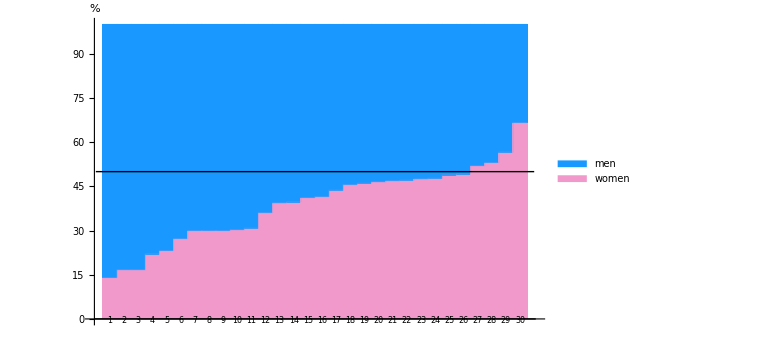
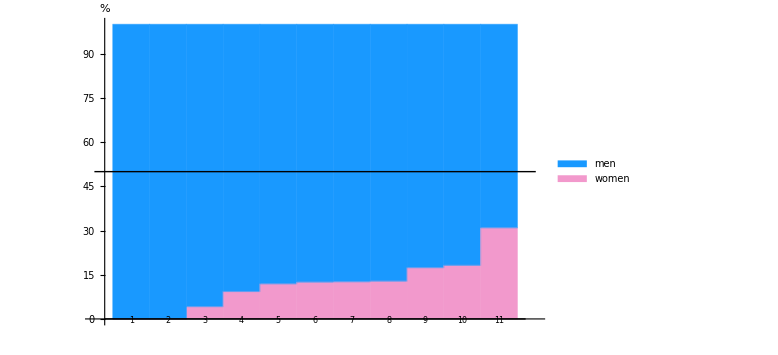
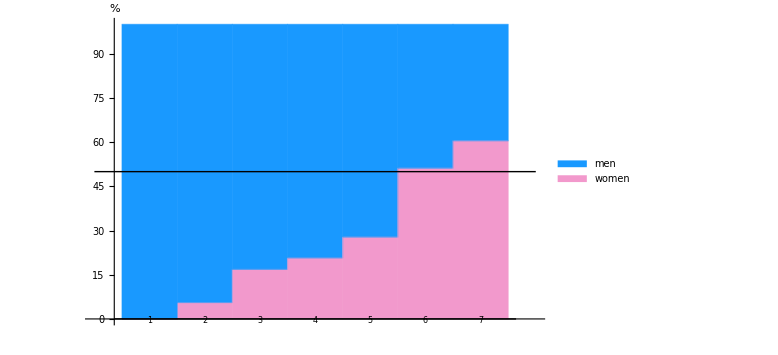
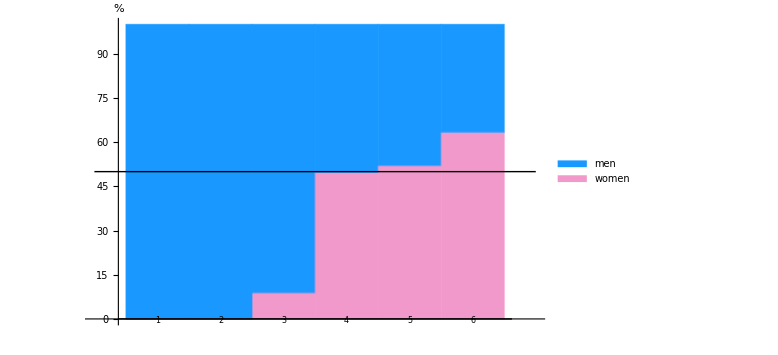
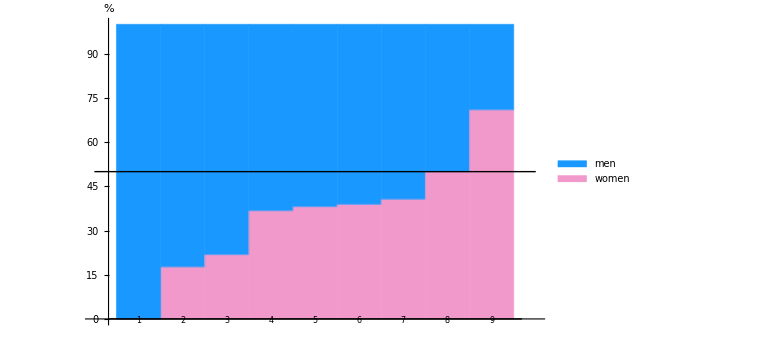
{-Graphics-sex distribution as bar chart
(30 studies included from 34)1 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
2 | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
3 | Perception of hearing loss in orchestral musicians    Gebel, E.; Jones, S. M.; Honaker, J. A. (2017)
4 | Sound exposures and hearing thresholds of symphony orchestra musicians    Royster, J. D.; Royster, L. H.; Killion, M. C. (1991)
5 | Hearing development in classical orchestral musicians. A follow-up study    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
6 | Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016)
7 | Effects of instrument type and orchestral position on hearing sensitivity for 0.25 to 20 kHz in the orchestral musician    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1985)
8 | Extended high frequency hearing sensitivity. A normative threshold study in musicians    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1986)
9 | Hearing assessment of classical orchestral musicians    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
10 | Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008)
11 | Acoustic trauma in classical music players    Morais, D; Benito, J. I.; Almaraz, A. (2007)
12 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
13 | Hearing loss in relation to sound exposure of professional symphony orchestra musicians    Schmidt, J. H.; Pedersen, E. R.; Paarup, H. M.; Christensen-Dalsgaard, J.; Andersen, T.; Poulsen, T.; Bælum, J. (2014)
14 | Hearing loss among classical-orchestra musicians    Toppila, E.; Koskinen, H.; Pyykkö, I. (2011)
15 | Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians    Wegner, R.; Wendlandt, P.; Poschadel, B.; Olma, K.; Szadkowski, D. (2000) | 16 | Review of orchestra musicians' hearing loss riskss    Eaton, S.; Gillis, H. (2002)
17 | The audiological health of horn players    Wilson, W. J.; O'Brien, I.; Bradley, A. P. (2013)
18 | Hearing ability in Danish symphony orchestra musicians    Obeling, L.; Poulsen, T. (1999)
19 | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
20 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
21 | Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras    Jansen, E. J.; Helleman, H. W.; Dreschler, W. A.; de Laat, J. A. (2009)
22 | Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds    Couth, S.; Prendergast, G.; Guest, H.; Munro, K. J.; Moore, D. R.; Plack, C. J.; Ginsborg, J.; Dawes, P. (2020)
23 | A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians    Dreyer, B.; Pottas, L.; Soer, M. E.; Graham, M. A.  (2023)
24 | Noise exposure and hearing loss in classical orchestra musicians    Russo, F. A.; Behar, A.; Chasin, M.; Mosher, S. (2013)
25 | Exposure to excessive sounds and hearing status in academic classical music students    Pawlaczyk-Łuszczyńska, M.; Zamojska-Daniszewska, M.; Dudarewicz, A.; Zaborowski, K. (2017)
26 | Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998)
27 | The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test    Gündüz, B.; Yıldırım Gökay, N.; Orhan, E.; Yılmaz, M. (2022)
28 | Evidence of noise-induced hearing loss among orchestral musicians    Backus, B. C.; Williamon, A. (2009)
29 | Prevalence of hearing loss among university music students    Comeau, G.; Koravand, A.; Swirp, M. (2018)
30 | Effect of musical training on masking paradigm    Devi, N.; Swathi, C. S. (2016)classical music,-Graphics-sex distribution as bar chart
(11 studies included from 18)1 | Audiological and electrophysiological assessment of professional pop/rock musicians    Samelli, A. G.; Matas, C. G.; Carvallo, R. M.; Gomes, R. F.; de Beija, C. S.; Magliaro, F. C.; Rabelo, C. M. (2012)
2 | Temporary threshold shift in rock-and-roll musicians    Jerger, J.; Jerger, S. (1970)
3 | Pop-rock musicians: assessment of their satisfaction provided by hearing protectors    Santoni, C. B.; Fiorini, A. C. (2010)
4 | Ototraumatic effects of hard rock music    Reddell, R. C.; Lebo, C. P. (1972)
5 | Hearing in nonprofessional pop/rock musicians    Schmuziger, N.; Patscheke, J.; Probst, R. (2006) | 6 | An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry    Schmuziger, N.; Patscheke, J.; Probst, R. (2007)
7 | Transient evoked otoacoustic emissions in rock musicians    Høydal, E. H.; Lein Størmer, C. C.; Laukli, E.; Stenklev, N. C. (2017)
8 | Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015)
9 | Study of the hearing of rock and roll musicians    Maia, J. R.; Russo, I. C. (2008)
10 | Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians    Halevi-Katz, D. N.; Yaakobi, E.; Putter-Katz, H. (2015)
11 | Assessment of hearing and hearing disorders in rock/jazz musicians    Kähärit, K.; Zachau, G.; Eklöf, M.; Sandsjö, L.; Möller, C. (2003)rock/pop/jazz,-Graphics-sex distribution as bar chart
(7 studies included from 9)1 | Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana    Setiawan, E. P.; Maryati, M. R. (2018)
2 | Valencia's cathedral church bell acoustics impact on the hearing abilities of bell ringers    García, L.; Parra, L.; Gomis, B. P.; Cavallé, L.; Pérez Guillén, V.; Pérez Garrigues, H.; Lloret, J. (2019)
3 | Noise-induced hearing loss among professional musicians    Pouryaghoub, G.; Mehrdad, R.; Pourhosein, S. (2017) | 4 | Hearing loss in steelband musicians    Juman, S.; Karmody, C. S.; Simeon, D. (2004)
5 | Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014)
6 | Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians    Ramma, L. (2021)
7 | Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018)traditional music,-Graphics-sex distribution as bar chart
(6 studies included from 6)1 | Auditory thresholds among military musicians: conventional and high frequency    Gonçalves, C. G.; Lacerda, A. B.; Zeigelboim, B. S.; Marques, J. M.; Luders, D.  (2013)
2 | Noise exposure and auditory thresholds of military musicians: a follow up study    Müller, R.; Schneider, J. (2018)
3 | Sound exposure and audiometric profile of military police band musicians    Lüders, D.; Da Silva Martins, K. R. R.; De Lacerda, A. B. M.; De Oliveira Gonçalves, C. G.; Heupa, A. B. (2017) | 4 | Hearing conservation program for marching band members: a risk for noise-induced hearing loss?    Jin, S. H.; Nelson, P. B.; Schlauch, R. S.; Carney, E. (2013)
5 | Hearing loss in British Army musicians    Patil, M. L.; Sadhra, S.; Taylor, C.; Folkes, S. E. (2013)
6 | Noise exposure and hearing protection in marching band students    Myers, E. (2021)military music,-Graphics-sex distribution as bar chart
(9 studies included from 10)1 | The influence of sound exposure onset and duration to the hearing loss prevalence in musicians    Widuri, A.; Gartiwa, G.; Pujiyanto, E. (2022)
2 | Acceptance of hearing protection aids in members of an instrumental and voice music band    Helena Mendes, M.; Catalani Morata, T; Mendes Marques, J. (2007)
3 | Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists    Hoffman, J. S.; Cunningham, D. R.; Lorenz, D. J. (2006)
4 | Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994) | 5 | Music students: conventional hearing thresholds and at high frequencies    Lüders, D.; Gonçalves, C. G.; Lacerda, A. B.; Ribas, Â.; Conto, J. d. (2014)
6 | Auditory electrophysiological and perceptual measures in student musicians with high sound exposure    Washnik, N. J. ; Bhatt, I. S.; Sergeev, A. V.; Prabhu, P.; Suresh, C. (2023)
7 | Hearing loss and mental health issues in amateur and professional musicians    Maghiar, M. J.;  Lawrence, B. J.; Mulders, W. H. A. M; Moyle, T. C.; Livings, I.; Jayakody, D. M. P.  (2023)
8 | ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?    Kikidis, D.; Vardonikolaki, A.; Zachou, Z.; Razou, A.; Pantos, P.; Bibas, A. (2020)
9 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)unknown, mixed genre}

```mathematica
genderAnalysis=.
genderAnalysis[l_List]:=Module[{n,temp,ngender,genderfrac,ngenderTitles,genderfracTitles},temp=Map[{StringSplit[#[[1]],"\n"][[1]],#[[2]]}&,l,{1}];
temp=If[#[[1]]=!="-",{StringSplit[#[[1]]," "],#[[2]]},Nothing]&/@temp;
n={{#[[1,1]],If[#[[1,2]]!="(?)",{StringCases[#[[1,2]],"("~~a__~~"f"->a],StringCases[#[[1,2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]},#[[2]]}&/@temp;ngenderTitles={ToExpression/@Flatten[#[[1]]],#[[2]]}&/@Select[n,#[[1,2,1,1]]!="?"&];
ngender=ngenderTitles[[All,1]];
genderfracTitles={{#[[1,2]]/(#[[1,2]]+#[[1,3]]),#[[1,3]]/(#[[1,2]]+#[[1,3]])}*100,#[[2]]}&/@ngenderTitles ;(*female, male portion*)
genderfracTitles=SortBy[genderfracTitles,#[[1,1]]&];
genderfrac=genderfracTitles[[All,1]];

datagenderAnalysis=genderfrac;

Labeled[
Labeled[
Show[
BarChart[genderfrac,
BarSpacing->0,
ChartLayout->"Stacked",
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"women","men"},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},
ChartLabels->{myStyle[If[EvenQ@#,"\n\n"~~ToString@#,"\n"~~ToString@#],8]&/@Range[Length@genderfrac],None},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}],

Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Style["sex distribution as bar chart\n("~~ToString[Length@ngender] ~~" studies included from "~~ ToString[Length@n]~~")",FontSize->18,FontFamily->fontStandard],Spacings->{1.3, 1.3}]

,
Grid[{Grid[#,Alignment->Left]&/@(If[OddQ[Length@Flatten@genderfracTitles[[All,2]]],{#[[1;;Floor[Length@Flatten@genderfracTitles[[All,2]]/2]]],#[[Ceiling[Length@Flatten@genderfracTitles[[All,2]]/2];;]]},{#[[1;;Length@Flatten@genderfracTitles[[All,2]]/2]],#[[Length@Flatten@genderfracTitles[[All,2]]/2+1;;]]}]&@Transpose[{myStyle/@Range[Length@Flatten@genderfracTitles[[All,2]]],myStyle/@Flatten@(StringReplace[ToLowerCase[#]," "->""]&/@Transpose[{#}]/.replaceTitle&/@genderfracTitles[[All,2]])}])}]
,Spacings->{1.3, 1.3}
]

(*}*)
]

genderAnalysis[#]&/@groups[[All,All,{4,1}]];
chartHistoGenderGroupsEN=Labeled[#[[1]],#[[2]], Top]&/@Transpose[{%,Style[#,FontFamily->fontStandard,FontSize->22,Bold]&/@ToLowerCase/@{"Classical Music","Rock/Pop/Jazz","Traditional Music","Military Music","Unknown, Mixed Genre"}}]
```

```mathematica
exportF[Transpose[{chartHistoGenderGroupsEN,{"Barchart Sex Portion Classic","Barchart Sex Portion Rock Pop Jazz","Barchart Sex Portion Traditional","Barchart Sex Portion Military Music","Barchart Sex Portion Unknown Genre"},{150,150,150,150,150}}]]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Classic.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Traditional.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Military Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Barchart Sex Portion Unknown Genre.svg}}}

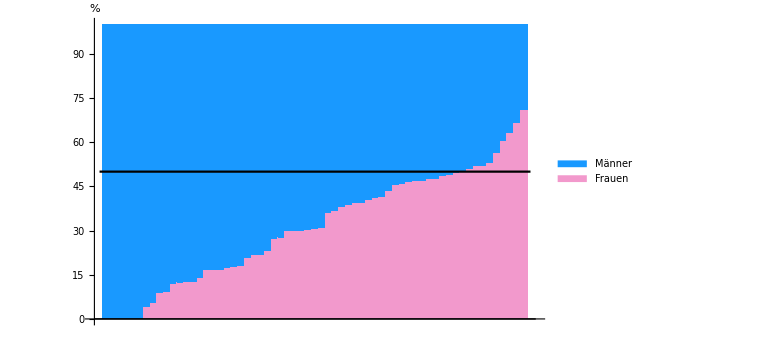
-Graphics-Geschlechterverteilung als Balkendiagramm
(63 Studien von 77 eingeschlossen)

{{{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg},{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg},{C:\Users\mona_\Desktop\Ausgabe\Geschlechtsverteilung alle Studien.svg}}}

{9,35.5726,0.000047201}

C:\Users\mona_\Desktop\Ausgabe\Pearson Chi2Test.txt

```mathematica
genderfrac=.
genderAnalysisDE[l_List]:=Module[{n,temp,ngender},temp=StringSplit[#,"\n"][[1]]&/@Rest[l];
temp=(StringSplit[#," "]&/@temp)/.{"-"}->Nothing;
n={#[[1]],If[#[[2]]!="(?)",{StringCases[#[[2]],"("~~a__~~"f"->a],StringCases[#[[2]],","~~b__~~"m"->b]},{{"?"},{"?"}}]}&/@temp;ngender=ToExpression/@Flatten[#]&/@Select[n,#[[2,1,1]]!="?"&];
genderfrac={#[[2]]/(#[[2]]+#[[3]]),#[[3]]/(#[[2]]+#[[3]])}*100&/@ngender;

(*{Show[ListPlot[genderfrac,AxesLabel->myStyleFunction[{"fraction women","fraction men"}],myTickStyle,PlotStyle->mycolor],Plot[.5,{x,0,0.7},PlotStyle->mycolor]],
Labeled[Histogram[genderfrac[[All,1]]*100,10,ChartStyle->mycolor],myStyle["Histogram of fraction female \n("~~ToString[Length@n] ~~" studies included from "~~ ToString[Length@l]~~")"]],FindDistribution[genderfrac[[All,1]]],*)

Labeled[
Show[
BarChart[SortBy[genderfrac,First],
BarSpacing->0,
ChartLayout->"Stacked",
Background->White,
ChartStyle->{"Hellrosa","Himmelblau"}/.colorlist,
ChartLegends->{"Frauen","Männer"},
ImageSize->Large,
AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},

LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black],LegendAppearance->{LegendMarkerSize->30,FontFamily->fontStandard}

],

Plot[50,{x,0,Length@ngender+1},PlotStyle->{Thick,Black}]
]

,Style["Geschlechterverteilung als Balkendiagramm\n("~~ToString[Length@ngender] ~~" Studien von "~~ ToString[Length@n]~~" eingeschlossen)",FontSize->18,FontFamily->fontStandard]]

(*}*)
]


chartHistoGenderDE=genderAnalysisDE[d[[All,4]]]

exportF[{{chartHistoGenderDE,"Geschlechtsverteilung alle Studien",900}}]




Needs["HypothesisTesting`"]
statTest=PearsonChiSquareTest[genderfrac[[All,1]],genderfrac[[All,2]],{"DegreesOfFreedom","TestStatistic","PValue"}]
(*Chi-Quadrat(4)=70.788,p<.001*)
Export[exPath~~"Pearson Chi2Test.txt",statTest]
```

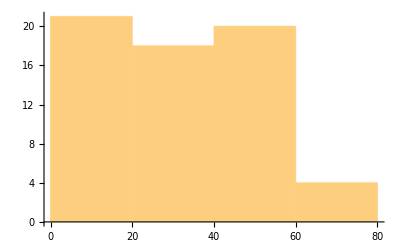
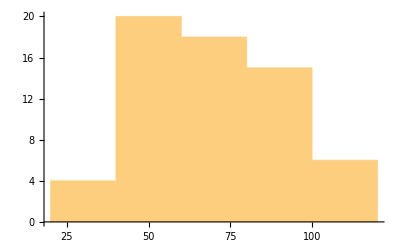

{UniformDistribution[{-0.0984364,70.9431}],MixtureDistribution[{0.648604,0.243883,0.107513},{NormalDistribution[57.0573,13.1651],NormalDistribution[85.6724,5.36226],NormalDistribution[100.004,0.0665762]}]}

```mathematica
Histogram/@Transpose@genderfrac
FindDistribution/@Transpose@genderfrac
```

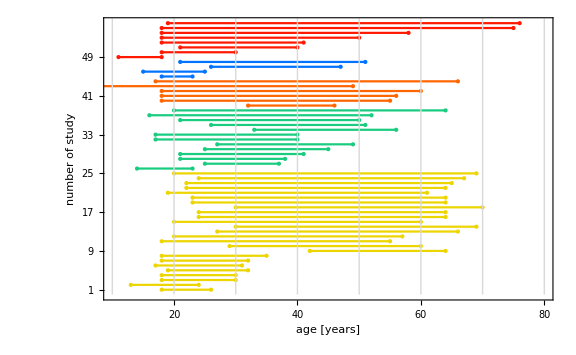
-Graphics-

-Graphics- classical music
         (25 studies included from 35)-Graphics- rock/pop/jazz
         (13 studies included from 18)-Graphics- traditional music
         (6 studies included from 9)-Graphics- military music
         (4 studies included from 6)-Graphics- unknown, mixed genre
         (8 studies included from 10)1 | Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds    Couth, S.; Prendergast, G.; Guest, H.; Munro, K. J.; Moore, D. R.; Plack, C. J.; Ginsborg, J.; Dawes, P. (2020)
2 | Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016)
3 | A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians    Dreyer, B.; Pottas, L.; Soer, M. E.; Graham, M. A.  (2023)
4 | The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test    Gündüz, B.; Yıldırım Gökay, N.; Orhan, E.; Yılmaz, M. (2022)
5 | Exposure to excessive sounds and hearing status in academic classical music students    Pawlaczyk-Łuszczyńska, M.; Zamojska-Daniszewska, M.; Dudarewicz, A.; Zaborowski, K. (2017)
6 | Prevalence of hearing loss among university music students    Comeau, G.; Koravand, A.; Swirp, M. (2018)
7 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
8 | Effect of musical training on masking paradigm    Devi, N.; Swathi, C. S. (2016)
9 | Perception of hearing loss in orchestral musicians    Gebel, E.; Jones, S. M.; Honaker, J. A. (2017)
10 | Noise-induced hearing loss and orchestral musicians    Westmore, G. A.; Eversden, I. D. (1981)
11 | The audiological health of horn players    Wilson, W. J.; O'Brien, I.; Bradley, A. P. (2013)
12 | Hearing loss in relation to sound exposure of professional symphony orchestra musicians    Schmidt, J. H.; Pedersen, E. R.; Paarup, H. M.; Christensen-Dalsgaard, J.; Andersen, T.; Poulsen, T.; Bælum, J. (2014)
13 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
14 | Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008)
15 | Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians    Wegner, R.; Wendlandt, P.; Poschadel, B.; Olma, K.; Szadkowski, D. (2000)
16 | Effects of instrument type and orchestral position on hearing sensitivity for 0.25 to 20 kHz in the orchestral musician    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1985)
17 | Extended high frequency hearing sensitivity. A normative threshold study in musicians    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1986)
18 | Sound exposures and hearing thresholds of symphony orchestra musicians    Royster, J. D.; Royster, L. H.; Killion, M. C. (1991)
19 | Hearing assessment of classical orchestral musicians    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
20 | Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras    Jansen, E. J.; Helleman, H. W.; Dreschler, W. A.; de Laat, J. A. (2009)
21 | Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998)
22 | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
23 | Hearing ability in Danish symphony orchestra musicians    Obeling, L.; Poulsen, T. (1999)
24 | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
25 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
26 | Temporary threshold shift in rock-and-roll musicians    Jerger, J.; Jerger, S. (1970)
27 | Beyond music: auditory temporary threshold shift in rock musicians after a heavy metal concert    Drake-Lee A. B. (1992) | 28 | Study of the hearing of rock and roll musicians    Maia, J. R.; Russo, I. C. (2008)
29 | Audiological and electrophysiological assessment of professional pop/rock musicians    Samelli, A. G.; Matas, C. G.; Carvallo, R. M.; Gomes, R. F.; de Beija, C. S.; Magliaro, F. C.; Rabelo, C. M. (2012)
30 | Pop-rock musicians: assessment of their satisfaction provided by hearing protectors    Santoni, C. B.; Fiorini, A. C. (2010)
31 | An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry    Schmuziger, N.; Patscheke, J.; Probst, R. (2007)
32 | Does pop music cause hearing damage?    Axelsson, A.; Lindgren, F. (1977)
33 | Hearing in pop musicians    Axelsson, A.; Lindgren, F. (1978)
34 | Hearing in pop/rock musicians: a follow-up study    Axelsson, A.; Eliasson, A.; Israelsson, B. (1995)
35 | Assessment of hearing and hearing disorders in rock/jazz musicians    Kähärit, K.; Zachau, G.; Eklöf, M.; Sandsjö, L.; Möller, C. (2003)
36 | Hearing in nonprofessional pop/rock musicians    Schmuziger, N.; Patscheke, J.; Probst, R. (2006)
37 | Transient evoked otoacoustic emissions in rock musicians    Høydal, E. H.; Lein Størmer, C. C.; Laukli, E.; Stenklev, N. C. (2017)
38 | Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians    Halevi-Katz, D. N.; Yaakobi, E.; Putter-Katz, H. (2015)
39 | Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014)
40 | Audiological and noise exposure findings among members of a Brazilian folklore music group    Carneiro Muniz, C. M. D.; da Silva, S. F. S.; Façanha, R. C.; Bassi-Dibai, D.; Silva, F. B.; Felipe, I. M. A.; Dias, R. D. S. (2021)
41 | An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012)
42 | Hearing loss in steelband musicians    Juman, S.; Karmody, C. S.; Simeon, D. (2004)
43 | Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians    Ramma, L. (2021)
44 | Valencia's cathedral church bell acoustics impact on the hearing abilities of bell ringers    García, L.; Parra, L.; Gomis, B. P.; Cavallé, L.; Pérez Guillén, V.; Pérez Garrigues, H.; Lloret, J. (2019)
45 | Noise exposure and hearing protection in marching band students    Myers, E. (2021)
46 | Hearing conservation program for marching band members: a risk for noise-induced hearing loss?    Jin, S. H.; Nelson, P. B.; Schlauch, R. S.; Carney, E. (2013)
47 | Hearing loss in British Army musicians    Patil, M. L.; Sadhra, S.; Taylor, C.; Folkes, S. E. (2013)
48 | Auditory thresholds among military musicians: conventional and high frequency    Gonçalves, C. G.; Lacerda, A. B.; Zeigelboim, B. S.; Marques, J. M.; Luders, D.  (2013)
49 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)
50 | Auditory electrophysiological and perceptual measures in student musicians with high sound exposure    Washnik, N. J. ; Bhatt, I. S.; Sergeev, A. V.; Prabhu, P.; Suresh, C. (2023)
51 | Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994)
52 | ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?    Kikidis, D.; Vardonikolaki, A.; Zachou, Z.; Razou, A.; Pantos, P.; Bibas, A. (2020)
53 | The influence of sound exposure onset and duration to the hearing loss prevalence in musicians    Widuri, A.; Gartiwa, G.; Pujiyanto, E. (2022)
54 | Music students: conventional hearing thresholds and at high frequencies    Lüders, D.; Gonçalves, C. G.; Lacerda, A. B.; Ribas, Â.; Conto, J. d. (2014)
55 | Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists    Hoffman, J. S.; Cunningham, D. R.; Lorenz, D. J. (2006)
56 | Acceptance of hearing protection aids in members of an instrumental and voice music band    Helena Mendes, M.; Catalani Morata, T; Mendes Marques, J. (2007)

```mathematica
ageAnalysisGroups[l_List]:=Module[{agerange,agerangesorted,agerangeTitles,intervallist,plotstyleSet},
agerange={(StringSplit[#[[1]],"\n"]),#[[2]]}&/@#&/@l;
agerange=Map[Select[#,#[[1]]=!="-"&]&,Transpose/@myT[agerange[[All,All,1,1]],agerange[[All,All,2]]],{1}];
agerange= Map[{ToExpression/@(StringSplit[#[[1]],{"-","–"}]),#[[2]]}&,agerange,{2}];
agerange= Map[{#[[1,2]]-#[[1,1]],#[[1,1]],#[[1,2]],#[[2]]}&,agerange,{2}];
agerangesorted=Map[SortBy[#,First]&,agerange,{1}];
agerangeTitles=agerangesorted[[All,All,-1]];
intervallist=Map[Interval[{#[[2]],#[[3]]}]&,agerangesorted,{2}];

plotstyleSet=Table[#[[1]],Length@#[[2]]]&/@Transpose[{colors[[1;;Length@intervallist]],intervallist}];

Labeled[
Labeled[

Show[


NumberLinePlot[
Flatten@intervallist,{x,10,80},
TicksStyle->Directive[FontFamily->fontStandard,fontSize],
ImageSize->Large,
PlotStyle->Flatten@plotstyleSet,

Frame->True,
FrameTicks->{{Range[1,Length@Flatten@intervallist,2],Range[2,Length@Flatten@intervallist,2]},
{Range[0,90,10],Automatic}},
FrameTicksStyle->{Directive[FontFamily->fontStandard,FontSize->10,Black],Directive[FontFamily->fontStandard,FontSize->18,Black]},
FrameLabel->(Style[#,FontFamily->fontStandard,FontSize->18,Black]&/@{"age [years]","number of study"})
],

Graphics[{ColorConvert[LightGray,"CMYK"],#}]&/@(Map[Line[{{#[[1]],0},{#[[1]],#[[2]]}}]&,Transpose@{Range[10,80,10],Table[Length[Flatten@intervallist]+1,Length@Range[10,80,10]]}])(*,
Graphics[{Thick,#}]&/@{Line[{{2,0},{2,40}}],Line[{{2,40},{95,40}}],Line[{{85,40},{85,0}}]}*)
]
,

Row[Row/@Transpose[{Table[Graphics[{i,Rectangle[]},ImageSize->30],{i,colors[[1;;5]]}],Style[#,FontFamily->fontStandard,FontSize->18]&/@ToLowerCase/@{" Classical Music\n         ("~~ToString[Length@intervallist[[1]]] ~~" studies included from "~~ ToString[Length@l[[1]]]~~")"," Rock/Pop/Jazz\n         ("~~ToString[Length@intervallist[[2]]] ~~" studies included from "~~ ToString[Length@l[[2]]]~~")"," Traditional Music\n         ("~~ToString[Length@intervallist[[3]]] ~~" studies included from "~~ ToString[Length@l[[3]]]~~")"," Military Music\n         ("~~ToString[Length@intervallist[[4]]] ~~" studies included from "~~ ToString[Length@l[[4]]]~~")"," Unknown, Mixed Genre\n         ("~~ToString[Length@intervallist[[5]]] ~~" studies included from "~~ ToString[Length@l[[5]]]~~")"}}],"\n"],Right,Spacings->{2,2}],

Grid[{Grid[#,Alignment->Left]&/@({#[[1;;27]],#[[28;;56]]}&@Transpose[{myStyle[#,13,"Calibri"]&/@Range[Length@Flatten@agerangeTitles],Flatten@(myStyle/@StringReplace[ToLowerCase[#]," "->""]&/@Transpose[{#}]/.replaceTitle&/@agerangeTitles)}])}]
]

]
chartAge=ageAnalysisGroups[Map[Transpose,Transpose[{groups[[All,All,5]],groups[[All,All,1]]}],{1}]]
```

```mathematica
exportF[{{chartAge,"Distribution of Age Ranges",600}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg},{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg},{C:\Users\mona_\Desktop\Ausgabe\Distribution of Age Ranges.svg}}}

```mathematica
ageAnalysisGroupsDE[l_List]:=Module[{agerange,agerangesorted,intervallist,plotstyleSet,chart},agerange=(StringSplit[#,"\n"]&/@#)&/@l;
agerange=StringSplit[#,{"-","–"}]&/@(Select[First/@#,#!="-"&&#!="?"&]&/@agerange);
agerange=Map[ToExpression,agerange,{2}];
agerange=Map[{#[[2]]-#[[1]],#[[1]],#[[2]]}&,agerange/.Null->10,{2}];
agerangesorted=SortBy[#,First][[All,2;;3]]&/@agerange;
intervallist=Map[Interval[{#[[1]],#[[2]]}]&,agerangesorted,{2}];
plotstyleSet=Table[#[[1]],Length@#[[2]]]&/@Transpose[{colors[[1;;Length@intervallist]],intervallist}];


chart=Labeled[

Show[


NumberLinePlot[
Flatten@intervallist,{x,10,80},
ImageSize->Large,
PlotStyle->Flatten@plotstyleSet,

Frame->True,
FrameTicks->{{Automatic,Automatic},
{Range[0,90,10],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->(Style[#,FontFamily->fontStandard,FontSize->18,Black]&/@{"Alter in Jahren","Anzahl"})
],

Graphics[{ColorConvert[LightGray,"CMYK"],#}]&/@(Map[Line[{{#[[1]],0},{#[[1]],#[[2]]}}]&,Transpose@{Range[10,80,10],Table[Length[Flatten@intervallist]+1,Length@Range[10,80,10]]}])(*,
Graphics[{Thick,#}]&/@{Line[{{2,0},{2,40}}],Line[{{2,40},{95,40}}],Line[{{85,40},{85,0}}]}*)
]
,

Row[Row/@Transpose[{Table[Graphics[{i,Rectangle[]},ImageSize->30],{i,colors[[1;;5]]}],Style[#,FontFamily->fontStandard,FontSize->18]&/@{" klassische Musik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[1]]] ~~" von "~~ ToString[Length@l[[1]]]~~")"," Rock/Pop/Jazz\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[2]]] ~~" von "~~ ToString[Length@l[[2]]]~~")"," traditionelle Musik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[3]]] ~~" von "~~ ToString[Length@l[[3]]]~~")"," Militärmusik und Marschmusik\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[4]]] ~~" von "~~ ToString[Length@l[[4]]]~~")"," unbekanntes Genre\n         (eingeschlossene Studien: "~~ToString[Length@intervallist[[5]]] ~~" von "~~ ToString[Length@l[[5]]]~~")"}}],"\n"],Right,Spacings->{1, 2}];

Rasterize[chart,ImageResolution->600]
]


chartAgeDE=ageAnalysisGroupsDE[groups[[All,All,5]]]
exportF[{{chartAgeDE,"Verteilung der Altersspannen",600}}]
```

-Graphics-

{{{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg},{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg},{C:\Users\mona_\Desktop\Ausgabe\Verteilung der Altersspannen.svg}}}

{5.,1.,5.,5.,5.,0.4,5.,5.,5.,1.,1.,5.,10.,5.,11.,6.,5.,16.,10,0.5,8.,2.,8.,1.,10.,5.,3.,5.,1.,10.,3.,7.,2.,2.,1.,0.,5.}

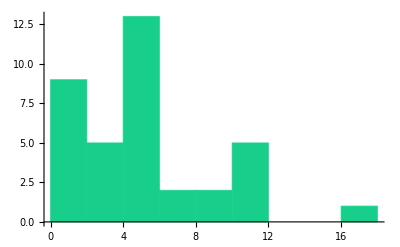
-Graphics-Histogram of years of practice
(37 studies included from 79)

```mathematica
yOfPractice=ToExpression/@Select[StringSplit[#,"\n"][[1]]&/@Rest[ToString/@d[[All,6]]],DigitQ[Characters[#][[1]]]&]
Labeled[Histogram[yOfPractice,10,myTickStyle,ChartStyle->mycolor,Ticks->{Range[0,17,2],Automatic}],myStyle["Histogram of years of practice\n("~~ToString[Length@yOfPractice] ~~" studies included from "~~ ToString[Length@d]~~")"]]
```

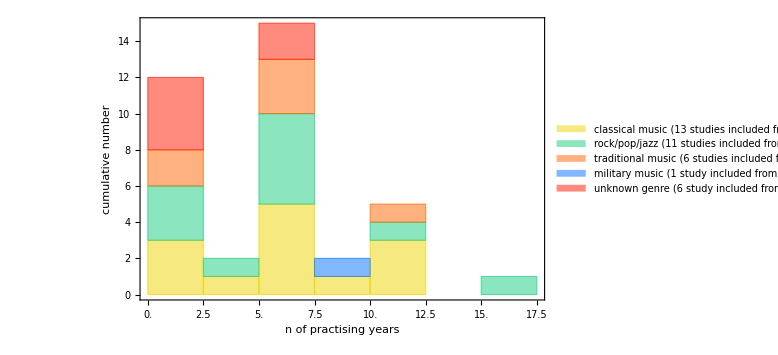

{{{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogram of minimal years as practising musician.svg}}}

```mathematica
yOfPractice=Map[ToString,groups[[All,All,6]],{2}];
yOfPractice=Map[StringSplit[#,"\n"][[1]]&,yOfPractice,{2}];
yOfPractice=Map[Select[#,DigitQ[Characters[#][[1]]]&]&,yOfPractice];
yOfPractice=Map[ToExpression,yOfPractice,{2}];

chartPracticeY=
Histogram[
yOfPractice,{2.5},myTickStyle,ChartLayout->"Stacked",ImageSize->Large,

Frame->True,FrameTicks->{{Automatic,All},
{Table[i,{i,0,18, 2.5}],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->{"n of practising years","cumulative number"},
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22,Black],

ChartStyle->colors,
ChartLegends->ToLowerCase/@{"Classical Music"~~"\n("~~ToString[Length@yOfPractice[[1]]] ~~" studies included from "~~ ToString[Length@groups[[1]]]~~")", "Rock/Pop/Jazz"~~"\n("~~ToString[Length@yOfPractice[[2]]] ~~" studies included from "~~ ToString[Length@groups[[2]]]~~")","Traditional Music"~~"\n("~~ToString[Length@yOfPractice[[3]]] ~~" studies included from "~~ ToString[Length@groups[[3]]]~~")","Military Music"~~"\n("~~ToString[Length@yOfPractice[[4]]] ~~" study included from "~~ ToString[Length@groups[[4]]]~~")","Unknown Genre"~~"\n("~~ToString[Length@yOfPractice[[5]]] ~~" study included from "~~ ToString[Length@groups[[5]]]~~")"},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20 ,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]


exportF[{{chartPracticeY,"Histogram of minimal years as practising musician",600}}]
```

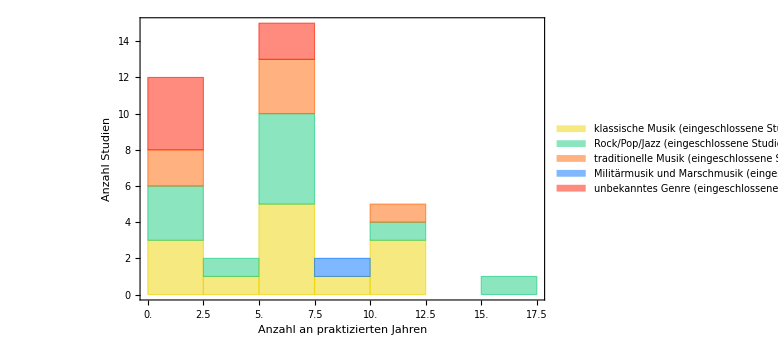

{{{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg},{C:\Users\mona_\Desktop\Ausgabe\Histogramm für minimale Spieljahresanzahl.svg}}}

```mathematica
yOfPractice=Map[ToString,groups[[All,All,6]],{2}];
yOfPractice=Map[StringSplit[#,"\n"][[1]]&,yOfPractice,{2}];
yOfPractice=Map[Select[#,DigitQ[Characters[#][[1]]]&]&,yOfPractice];
yOfPractice=Map[ToExpression,yOfPractice,{2}];

chartPracticeYDE=
Histogram[
yOfPractice,{2.5},myTickStyle,ChartLayout->"Stacked",ImageSize->Large,

Frame->True,FrameTicks->{{Automatic,All},
{Table[i,{i,0,18, 2.5}],Automatic}},
FrameTicksStyle->Directive[FontFamily->fontStandard,FontSize->18,Black],
FrameLabel->{"Anzahl an praktizierten Jahren","Anzahl Studien"},
FrameStyle->Directive[FontFamily->fontStandard,FontSize->22,Black],

ChartStyle->colors,
ChartLegends->{"klassische Musik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[1]]] ~~" von "~~ ToString[Length@groups[[1]]]~~")", "Rock/Pop/Jazz"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[2]]] ~~" von "~~ ToString[Length@groups[[2]]]~~")","traditionelle Musik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[3]]] ~~" von "~~ ToString[Length@groups[[3]]]~~")","Militärmusik und Marschmusik"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[4]]] ~~" von "~~ ToString[Length@groups[[4]]]~~")","unbekanntes Genre"~~"\n(eingeschlossene Studien: "~~ToString[Length@yOfPractice[[5]]] ~~" von "~~ ToString[Length@groups[[5]]]~~")"},
LabelStyle->Directive[FontFamily->fontStandard,FontSize->20 ,Black],
LegendAppearance->{LegendMarkerSize->Scaled[.1],FontFamily->fontStandard}
]

exportF[{{chartPracticeYDE,"Histogramm für minimale Spieljahresanzahl",600}}]
```

```mathematica
(*poor data*)
com=Rest[d[[All,11]]];
npd=Length@com
nPoorpd=Length[Select[com,StringContainsQ[ToString@#,"poor"]&]]
nPoorPerc=nPoorpd/npd//N
Export[exPath~~"Poor Data.txt","all "~~ToString@npd~~"\npoor "~~ToString@nPoorpd~~"\npercent "~~ToString@nPoorPerc]
```

78

32

0.410256

C:\Users\mona_\Desktop\Ausgabe\Poor Data.txt

```mathematica
audiometryFrList= ToExpression/@ StringSplit["125,250,500,1000,2000,3000,4000,6000,8000,9000,10000,11200,12500,14000,16000",","];
nameresult[l_List]:=Module[{p},p=l[[1]]; Append[#,p]&/@l[[2]]];
nameresultList[l_List]:=Module[{p},p=l[[{1,3}]]; Append[#,p]&/@l[[2]]];
pos[v_]:=Module[{},Position[audiometryFrList,v]];
greenColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0.01+i*0.7/m,0,0.01+i 0.6/m,0}]]
redColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0,0.01+i*0.9/m,0.01+i 1/m,0}]]
yellowColorF[i_Integer,m_Integer]:=Module[{},CMYKColor[{0.01+i*0.1/m,0.01+i 0.1/m,0.01+i .9/m,0}]]
```

```mathematica
links=Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/literature%20list%20with%20title,%20author,%20DOI.xlsx"][[1]];
linksReplace=(Rest@links[[All,{1,4,2,8}]])/.{"","","",""}->Nothing;
replaceLink=StringReplace[ToLowerCase[#[[1]]]," "->""]->"["<>#[[1]]<>"    "<>#[[3]]<>" ("<>If[StringLength[ToString[#[[4]]]]>4,StringJoin[Characters[ToString[#[[4]]]][[1;;4]]],""]<>")]("<>#[[2]]<>")"&/@linksReplace;
replaceTitle=StringReplace[ToLowerCase[#[[1]]]," "->""]->#[[1]]<>"    "<>#[[3]]<>" ("<>If[StringLength[ToString[#[[4]]]]>4,StringJoin[Characters[ToString[#[[4]]]][[1;;4]]],""]<>")"&/@linksReplace;
```

```mathematica
graphRectangle[l_List]:=Module[{ex,r},ex=ToExpression/@Flatten[l][[1;;2]];r=ex[[1]]/ex[[2]];Graphics[{l[[3]],Rectangle[{0,0},{r,.15}],"Grün",Rectangle[{r,0},{1,.15}]}]/.colorlist]
graphRectangle[{{3},{16},"Zitronengelb"}]
```

-Graphics-

```mathematica
groups[[All,All,{1,10,4}]]
```

## Result Analysis

```mathematica
Length@Flatten[groups[[All,All,{1,-1}]],1]
```

84

```mathematica
Length@Rest@d[[All,{1,-1}]]
```

78

ToExpression::sntxi: Incomplete expression; more input is needed .

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0 encountered.

Max::nord: Invalid comparison with ComplexInfinity attempted.

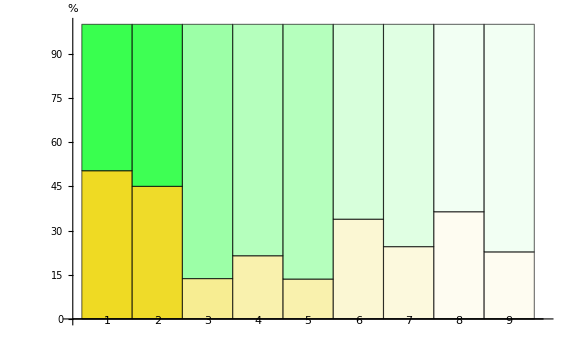
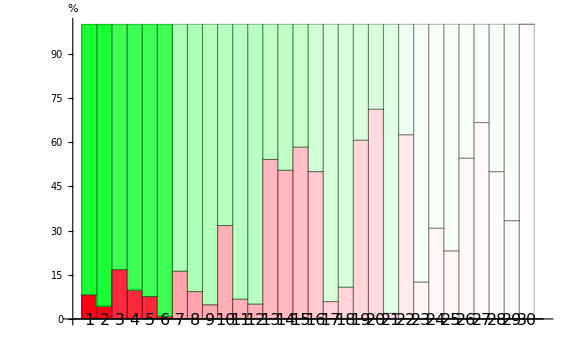
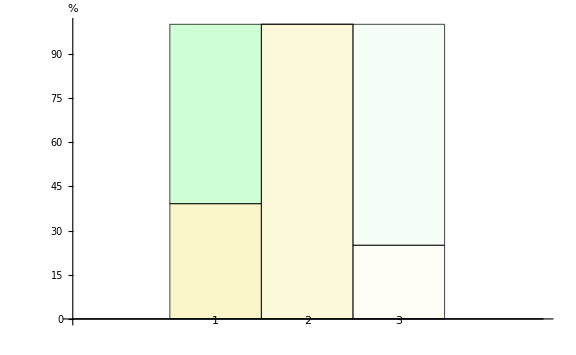
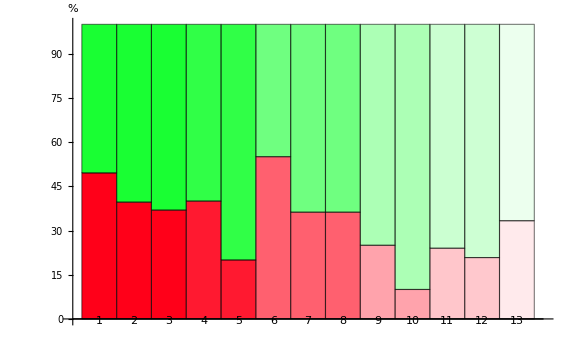
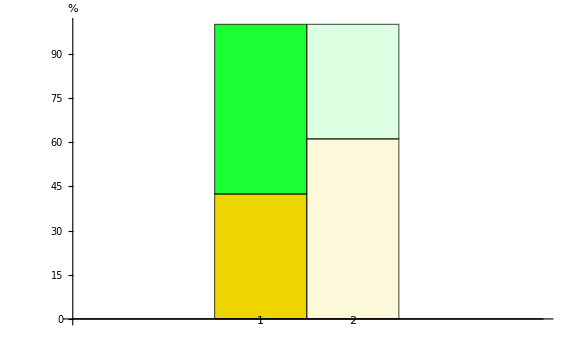
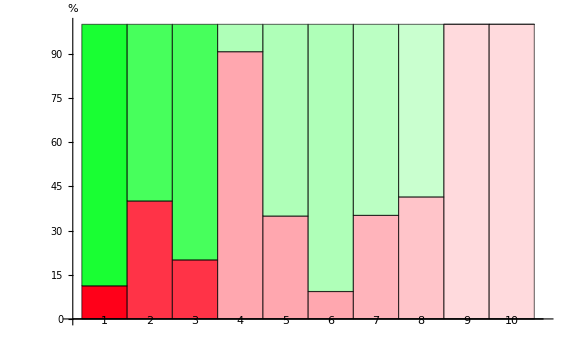
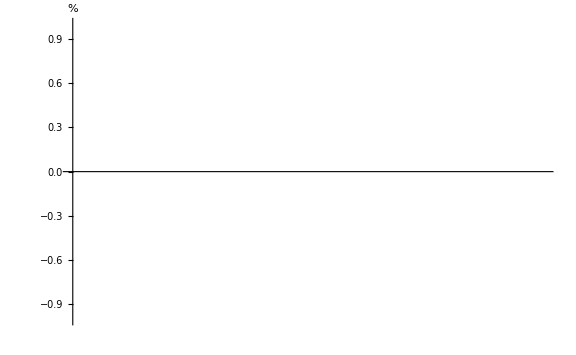
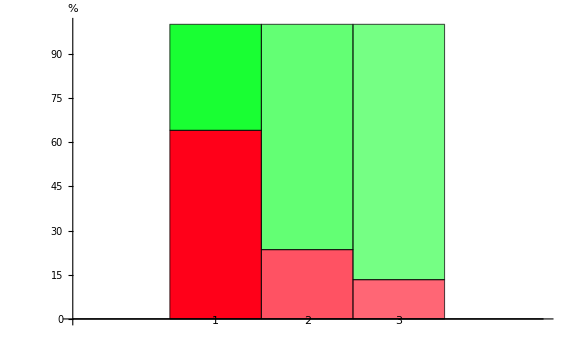
{-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | music students | 170 | 338 | notch | - | 6000 | Environmental factors in susceptibility to noise-induced hearing loss in student musicians    Phillips, S. L.; Shoemaker, U.; Mace, S. T.; Hodges, D. A. (2008)
2 | music students (classical music, 19 jazz) | 148 | 329 | notch >15 dB | r/l | 4000-6000 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
3 | music students | 23 | 168 | notch >15 dB | - | 4000-6000 | Exposure to excessive sounds and hearing status in academic classical music students    Pawlaczyk-Łuszczyńska, M.; Zamojska-Daniszewska, M.; Dudarewicz, A.; Zaborowski, K. (2017)
4 | symphony orchestra musicians | 27 | 126 | notches | l | 4000-6000 | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
5 | symphony orchestra musicians | 17 | 126 | notches | r | 4000-6000 | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
6 | orchestra musicians [ears reported for affected persons and sample size] | 23 | 68 | notches | - | - | Noise-induced hearing loss and orchestral musicians    Westmore, G. A.; Eversden, I. D. (1981)
7 | orchestra musicians | 13 | 53 | notch 15 dB | r+l | 3000-6000 | Review of orchestra musicians' hearing loss riskss    Eaton, S.; Gillis, H. (2002)
8 | adolescent musicians | 8 | 22 | notches | l | 3000-6000 | Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016)
9 | adolescent musicians | 5 | 22 | notches | r | 4000-6000 | Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016)-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | flute players | 17 | 392 | loss 20 dB | r+l | 4000-8000 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
2 | double bass players | 32 | 392 | loss | l | 4000-8000 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
3 | music students (classical music, 19 jazz) | 55 | 329 | loss | l | 6000 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
4 | music students (classical music, 19 jazz) | 32 | 329 | loss | r | 6000 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
5 | music students (classical music, 19 jazz) | 25 | 329 | loss | r+l | 6000 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
6 | music students (classical music, 19 jazz) | 3 | 329 | loss | r+l | 4000 | Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010)
7 | french horn players | 23 | 142 | loss | - | - | The audiological health of horn players    Wilson, W. J.; O'Brien, I.; Bradley, A. P. (2013)
8 | 7 musicians playing small strings, 3 woodwind players, 2 brasswind players and 1 percussionist | 13 | 140 | loss | - | 3000-8000 | Hearing assessment of classical orchestral musicians    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001)
9 | symphony orchestra musicians (88.9% are older musicians that have the loss) | 6 | 126 | loss >25 dB | - | - | Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013)
10 | musicians in 6 year follow-up who are 50-59 years | 39 | 123 | loss | - | 4000-6000 | The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983)
11 | orchestra musicians | 8 | 119 | loss >15 dB | l | 6000 | Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998)
12 | orchestra musicians | 6 | 119 | loss >15 dB | r | 6000 | Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998)
13 | strings from classical music orchestra (positively age correlated) | 59 | 109 | loss | l | 4000-6000 | Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008)
14 | orchestra musicians | 55 | 109 | loss >15 dB | - | - | Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008)
15 | orchestra musicians (theatre) | 56 | 96 | loss >20 dB | r+l/r/l | - | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
16 | male orchestra musicians (theatre) | 40 | 80 | loss >20 dB | r+l/r/l | - | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
17 | orchestra musicians [ears reported for affected persons and sample size]  | 4 | 68 | loss >20 dB | - | 4000 | Noise-induced hearing loss and orchestral musicians    Westmore, G. A.; Eversden, I. D. (1981)
18 | symphony orchestra members | 7 | 65 | loss | r+l | 4000 | Acoustic trauma in classical music players    Morais, D; Benito, J. I.; Almaraz, A. (2007)
19 | symphony orchestra members | 37 | 61 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
20 | symphony orchestra players | 42 | 59 | loss | r/l/r+l | 2000-8000 | Sound exposures and hearing thresholds of symphony orchestra musicians    Royster, J. D.; Royster, L. H.; Killion, M. C. (1991)
21 | music students (classical music) | 1 | 53 | loss | - | - | Prevalence of hearing loss among university music students    Comeau, G.; Koravand, A.; Swirp, M. (2018)
22 | symphony orchestra members — small string instrument group | 20 | 32 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
23 | female orchestra musicians (theatre) | 2 | 16 | loss >20 dB | r+l/r/l | - | Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989)
24 | members of orchestra | 4 | 13 | loss | r+l/r/l | ~4000-8000 | Hearing impairment among orchestral musicians    Woolford, D. H.;Carterette, E. C.; Morgan, D. E.  (1988)
25 | members of orchestra | 3 | 13 | loss >25 dB | r/l | ~4000-8000 | Hearing impairment among orchestral musicians    Woolford, D. H.;Carterette, E. C.; Morgan, D. E.  (1988)
26 | symphony orchestra members —  string instrument group | 6 | 11 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
27 | symphony orchestra members —  brass instrument group | 6 | 9 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
28 | symphony orchestra members — woodwind instrument group | 2 | 6 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011)
29 | symphony orchestra members | 3 | 6 | loss >25 dB | r+l | 4000-8000 | Perception of hearing loss in orchestral musicians    Gebel, E.; Jones, S. M.; Honaker, J. A. (2017)
30 | symphony orchestra members — percussion group | 3 | 3 | loss > 25 dB | r+l/r/l | predominately 6000 | Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011),-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | rock musicians | 9 | 23 | notch | - | 4000-6000 | Study of the hearing of rock and roll musicians    Maia, J. R.; Russo, I. C. (2008)
2 | 16 non-professional musicians | 16 | 16 | notch | r+l | 6000 | An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry    Schmuziger, N.; Patscheke, J.; Probst, R. (2007)
3 | heavy metal band members | 1 | 4 | notch | r+l | 6000 | Beyond music: auditory temporary threshold shift in rock musicians after a heavy metal concert    Drake-Lee A. B. (1992)-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | rock musicians | 41 | 111 | loss | - | - | Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015)
2 | male rock musicians | 44 | 111 | loss | - | - | Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015)
3 | female rock musicians | 55 | 111 | loss | - | - | Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015)
4 | band of dance members | 40 | 100 | loss (slight to moderate) | l | - | An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012)
5 | band of dance members | 20 | 100 | loss (slight to moderate) | r+l | - | An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012)
6 | pop musicians | 38 | 69 | loss >20 dB | r/l | - | Does pop music cause hearing damage?    Axelsson, A.; Lindgren, F. (1977)
7 | pop musicians | 25 | 69 | loss >20 dB | r+l/r/l | 3000-8000 | Pop music and hearing    Axelsson, A.; Lindgren, F. (1981)
8 | pop musicians | 25 | 69 | loss > 20 dB | r/l | 3000-8000 | Hearing in pop musicians    Axelsson, A.; Lindgren, F. (1978)
9 | pop musicians | 10 | 40 | loss > 20 dB | r/l | 4000-6000 | Hearing in pop/rock musicians: a follow-up study    Axelsson, A.; Eliasson, A.; Israelsson, B. (1995)
10 | pop musicians | 4 | 40 | loss > 20 dB | r+l | 4000-6000 | Hearing in pop/rock musicians: a follow-up study    Axelsson, A.; Eliasson, A.; Israelsson, B. (1995)
11 | rock musicians | 6 | 25 | loss >20 dB | - | - | Hearing loss in rock-and-roll musicians    Speaks, C.; Nelson, D.; Ward, W. D. (1970)
12 | rock & pop musicians | 5 | 24 | loss | r+l | 3000-6000 | Pop-rock musicians: assessment of their satisfaction provided by hearing protectors    Santoni, C. B.; Fiorini, A. C. (2010)
13 | rock band members | 3 | 9 | loss >30 dB | - | 2000-8000 | Temporary threshold shift in rock-and-roll musicians    Jerger, J.; Jerger, S. (1970),-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | traditional and/or pop musicians | 53 | 125 | notches | r+l/r/l | - | Noise-induced hearing loss among professional musicians    Pouryaghoub, G.; Mehrdad, R.; Pourhosein, S. (2017)
2 | musicians in a Brazilian dance group | 11 | 18 | notch | - | - | Audiological and noise exposure findings among members of a Brazilian folklore music group    Carneiro Muniz, C. M. D.; da Silva, S. F. S.; Façanha, R. C.; Bassi-Dibai, D.; Silva, F. B.; Felipe, I. M. A.; Dias, R. D. S. (2021)-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | violin players | 14 | 125 | loss (not significant to other instrument groups) | l | - | Noise-induced hearing loss among professional musicians    Pouryaghoub, G.; Mehrdad, R.; Pourhosein, S. (2017)
2 | band of dance members | 40 | 100 | loss (slight to moderate) | l | - | An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012)
3 | band of dance members | 20 | 100 | loss (slight to moderate) | r+l | - | An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012)
4 | students and teachers from Valencia drum school | 39 | 43 | loss 10 dB | - | 125 | Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018)
5 | students and teachers from Valencia drum school | 15 | 43 | loss >25 dB | r+l/r/l | - | Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018)
6 | students and teachers from Valencia drum school | 4 | 43 | loss 15 dB | - | 125 | Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018)
7 | Jegog players (traditional instrument of Indonesia) | 13 | 37 | loss >25 dB | - | - | Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana    Setiawan, E. P.; Maryati, M. R. (2018)
8 | traditional steel band musicians | 12 | 29 | loss >20 dB | - | 3000-8000 | Hearing loss in steelband musicians    Juman, S.; Karmody, C. S.; Simeon, D. (2004)
9 | 18 Daf Musicians | 18 | 18 | loss >16 dB | - | 3000 | Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014)
10 | 18 Daf Musicians | 18 | 18 | loss >16 dB | - | 250 | Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014),-Graphics-{}-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | musicians from police band | 32 | 50 | loss | - | - | Auditory thresholds among military musicians: conventional and high frequency    Gonçalves, C. G.; Lacerda, A. B.; Zeigelboim, B. S.; Marques, J. M.; Luders, D.  (2013)
2 | musicians from police band | 8 | 34 | loss >25 dB | r+l/r/l | ~6000 | Sound exposure and audiometric profile of military police band musicians    Lüders, D.; Da Silva Martins, K. R. R.; De Lacerda, A. B. M.; De Oliveira Gonçalves, C. G.; Heupa, A. B. (2017)
3 | marching band members | 4 | 30 | loss > 20 dB | - | - | Noise exposure and hearing protection in marching band students    Myers, E. (2021),-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | high school band members | 8 | 20 | notch | r+l | 4000-6000 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)
2 | high school band members | 5 | 20 | notch | r | 4000-6000 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)
3 | middle school band members | 4 | 11 | notch | r+l | 4000-6000 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)
4 | high school band members | 2 | 11 | notch | r | 4000-6000 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)
5 | high school band members | 1 | 11 | notch | l | 4000-6000 | Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020)-Graphics-bar number | affected group | affected persons | total sample size | finding | ear side | frequency range [Hz] | publication
1 | percussionists | 119 | 304 | loss >25 dB | r+l | 250-8000 | Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists    Hoffman, J. S.; Cunningham, D. R.; Lorenz, D. J. (2006)
2 | musicians | 123 | 241 | loss | - | - | Screening and prevalence of hearing loss in professional musicians    Laraqui, S.; Manar, N.; Laraqui, O.; Laraqui, F.; Laraqui Hossini, C. E. H. (2022)
3 | music students (mixed genre) | 12 | 64 | loss > 20 dB | r+l/r/l | 3000-6000 | Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994)
4 | music students (mixed genre) | 10 | 64 | loss >20 dB | r+l/r/l | 3000-8000 | Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994)
5 | music students | 3 | 42 | loss >25 dB | r+l/r/l | 6000-8000 | Music students: conventional hearing thresholds and at high frequencies    Lüders, D.; Gonçalves, C. G.; Lacerda, A. B.; Ribas, Â.; Conto, J. d. (2014)
6 | city band members | 9 | 36 | loss >25 dB | r+l | 4000-6000 | Acceptance of hearing protection aids in members of an instrumental and voice music band    Helena Mendes, M.; Catalani Morata, T; Mendes Marques, J. (2007)
7 | musicians from Yogyakarta, Indonesia | 20 | 35 | loss | - | - | The influence of sound exposure onset and duration to the hearing loss prevalence in musicians    Widuri, A.; Gartiwa, G.; Pujiyanto, E. (2022)}

```mathematica
resGroups=Map[
{#[[1]]
,StringSplit[#[[2]],",__"]
,ToExpression[StringSplit[StringSplit[#[[3]],"\n"][[1]]," "][[1]]]/.$Failed->"not reported"
,If[StringContainsQ[#[[3]],"?"|"-"],"-",StringReplace[myStringSplit[#[[3]],{"\n"," "}][[1,2]],{"("->"",")"->"",","->", "}]]
,If[NumberQ[#[[5]]],#[[5]],"-"],#[[-1]]/. {1.-> "yes",2.->"n/a",0.->"no"}}&,groups[[All,All,{1,10,4,5,6,-1}]],{2}];

(*Title, results, sex, minimum years of practice, age correction*)

resGroups=Map[{#[[1]],StringSplit[#,"__"]&/@#[[2]],#[[3;;-1]]}&,resGroups,{2}];
resGroupsAppend=.
resGroupsAppend[l_List]:=Module[{lcopy,results},lcopy=l[[1;;2]];results=l[[-1]];Append[lcopy,#]&/@results]
resGroups=Map[resGroupsAppend/@myTake[#,{1,-1,2}]&,resGroups,{1}];
resGroups=Map[Flatten[#,1]&,resGroups,{1}];


resGroups=Map[Which[StringContainsQ[#[[-1,1]],"loss"],"loss"->#,StringContainsQ[#[[-1,1]],"notch"],"notch"->#,StringContainsQ[#[[-1,1]],"normal"],"normal"->#]&,resGroups ,{2}];

resGroups=Map[GroupBy[#,Keys]&,resGroups/.Null->Nothing ,{1}];
resGroups=Map[Values,resGroups ,{3}];

resGroups=Map[{#[[1;;2]],MapAt[If[#!="-",StringCases[#,DigitCharacter..]&/@StringSplit[#,"/"],#]&,#[[-1]],5]}&,resGroups ,{3}];


resGroups=Map[Which[
StringContainsQ[#[[-1,1]],"loss"],{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[Append[#,"Leuchtrot"]],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

,StringContainsQ[#[[-1,1]],"notch"],
{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[Append[#,"Zitronengelb"]],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

,StringContainsQ[#[[-1,1]],"normal"],
{#[[1]],MapAt[If[ListQ[#]==True,{Labeled[graphRectangle[{{0},{#[[2]]},"Grün"}],myStyle[Flatten[#][[1]]<>"/"<>Flatten[#][[2]]],Right],ToExpression[Flatten[#][[2]]]},#]&,#[[-1]],5]}

]&,resGroups ,{3}];

getKey[l_Association]:=Module[{i},i=l[[{"normal","notch","loss"}]];Values[i]]
gitHubgridContent=getKey[#]&/@resGroups;
gitHubgridContent=Map[Flatten[#[[{-1,1}]],1]&,gitHubgridContent,{3}];

portionAffected=Map[#[[1;;-2]]&,gitHubgridContent,{3}];


portionAffectedPlot=Map[Select[#,ListQ[#[[5]]]&]&,portionAffected[[All,{2,3}]],{2}][[All,All,All,5,1,2]];
portionAffectedPlot=ToExpression/@Map[StringSplit[ToString@#,"/"]&,portionAffectedPlot,{3}];
portionAffectedPlot=Map[ReverseSortBy[#,Last]&,portionAffectedPlot,{2}];
MaxListportionAffectedPlot=Map[Max[Join[#[[1]],#[[2]]][[All,2]]]&,portionAffectedPlot,{1}];
Transpose@{portionAffectedPlot,MaxListportionAffectedPlot};
portionAffectedPlot=Map[(a=#[[-1]];Append[#,a]&/@#&/@#[[1]])&,%,{1}];
portionAffectedPlot=Map[{(#[[1]]/#[[2]])100,(1-(#[[1]]/#[[2]]))100,#[[2]]/#[[3]]}&,portionAffectedPlot,{3}];

portionAffectedPlot=Map[Transpose,Transpose[{portionAffectedPlot,Map[Length,portionAffectedPlot,{2}]}],{1}];
portionAffectedPlot=Map[Flatten[#,1]&,portionAffectedPlot,{2}];

styleportionAffectedPlotNotch[o_List]:=Module[{},{Style[o[[1]],Opacity[o[[3]],colors[[1]]]],Style[o[[2]],Opacity[o[[3]],"Grün"/.colorlist]]}]
styleportionAffectedPlotLoss[o_List]:=Module[{},{Style[o[[1]],Opacity[o[[3]],"Reines Rot"/.colorlist]],Style[o[[2]],Opacity[o[[3]],"Grün"/.colorlist]]}]

portionAffectedPlotNotch= Map[BarChart[If[#!={},styleportionAffectedPlotNotch[#],Null]&/@#[[1;;-2]],ChartLayout->"Stacked",ImageSize->Large,ChartLabels->{If[#[[-1]]>25,Style[#,FontSize->16]&/@(If[EvenQ[#],"\n"<>ToString[#],#]&/@Range[#[[-1]]]),Range[#[[-1]]]],None},BarSpacing->0,AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black]]&,portionAffectedPlot,{2}];
portionAffectedPlotLoss=Map[BarChart[If[#!={},styleportionAffectedPlotLoss[#],Null]&/@#[[1;;-2]],ChartLayout->"Stacked",ImageSize->Large,ChartLabels->{If[#[[-1]]>25,Style[#,FontSize->16,FontFamily->fontStandard]&/@(If[EvenQ[#],"\n"<>ToString[#],#]&/@Range[#[[-1]]]),Range[#[[-1]]]],None},BarSpacing->0,AxesLabel->{None,Style["%",FontSize->25,FontFamily->"Arial"]},LabelStyle->Directive[FontFamily->fontStandard,FontSize->20,Black]]&,portionAffectedPlot,{2}];
portionAffectedPlotLoss=Transpose[{portionAffectedPlotNotch[[All,1]],portionAffectedPlotLoss[[All,2  ]]}];

portionAffectedPlotLegend=Map[Select[#,ListQ[#[[5]]]&]&,portionAffected[[All,{2,3}]],{2}][[All,All,All,{4,5,1,3,2,6}]];
portionAffectedPlotLegend[[All,All,All,2]]=ToExpression/@Map[StringSplit[ToString@#,"/"]&,portionAffectedPlotLegend[[All,All,All,2,1,2]],{3}];
portionAffectedPlotLegend=Map[ReverseSortBy[#,Last[#[[2]]]&]&,portionAffectedPlotLegend,{2}];
portionAffectedPlotLegend[[All,All,All,-1]]=Map[StringReplace[ToLowerCase[#]," "->""]&,portionAffectedPlotLegend[[All,All,All,-1]],{2}];

portionAffectedPlotLegend=Map[(Prepend[{#},Range[Length@#]])&,portionAffectedPlotLegend/.replaceTitle,{2}];
portionAffectedPlotLegend=Map[(Transpose),portionAffectedPlotLegend,{2}];
portionAffectedPlotLegend=Map[Flatten,portionAffectedPlotLegend,{3}];
portionAffectedPlotLegend=Map[Style[TableForm[#,TableHeadings->{None,{"bar number","affected group","affected persons","total sample size","finding","ear side","frequency range [Hz]","publication"}}],FontSize->fontSize,FontFamily->fontStandard]&,portionAffectedPlotLegend,{2}];

labeledportionAffectedPlot=Map[Transpose,Transpose[{portionAffectedPlotLoss,portionAffectedPlotLegend}],{1}];
labeledportionAffectedPlot=Map[Labeled[#[[1]],#[[2]],Bottom]&,labeledportionAffectedPlot,{2}];
labeledportionAffectedPlot=Labeled[#[[1]],#[[2]],Bottom]&/@labeledportionAffectedPlot
```

```mathematica
exportFPNG[Transpose[{ReplacePart[labeledportionAffectedPlot,{4,1}->""],{"Portion Affected Persons Barchart and Table Classical Music","Portion Affected Persons Barchart and Table Rock Pop Jazz","Portion Affected Persons Barchart and Table Traditional Music","Portion Affected Persons Barchart and Table Military Music","Portion Affected Persons Barchart and Table Unknown Genre"},Table[400,5]}]]
```

{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music 400 dpi.png},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre 400 dpi.png}}

```mathematica
exportFSVG[Transpose[{ReplacePart[labeledportionAffectedPlot,{4,1}->""],{"Portion Affected Persons Barchart and Table Classical Music","Portion Affected Persons Barchart and Table Rock Pop Jazz","Portion Affected Persons Barchart and Table Traditional Music","Portion Affected Persons Barchart and Table Military Music","Portion Affected Persons Barchart and Table Unknown Genre"}}]]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Classical Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Traditional Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Military Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Portion Affected Persons Barchart and Table Unknown Genre.svg}}}

#### GitHub Summary Table Export

```mathematica
gitHubgridContent
```

```mathematica
temp=Map[Prepend[#,If[ListQ[#[[5]]],#[[5,2]],#[[-1,1]]]]&,gitHubgridContent,{3}];
temp=Map[ReverseSortBy[#,First]&,temp,{2}];

temp=Map[{#[[{7,1}]],#[[-1,2]],#[[{2,3}]],#[[-1,-1]],#[[{4,6,5}]],#[[-1,-2]]}&,temp,{3}];

temp[[All,All,All,1,1]]=Map[StringReplace[ToLowerCase[#]," "->""]&,temp[[All,All,All,1,1]],{2}]/.replaceLink;

i=0;
temp[[All,All,All,-2,2]]=Map[If[ListQ[#],(i++;Export[exPath~~"\\figures for summary table\\"~~IntegerString[i,10,3]~~".png",Rasterize[#[[1,1]],ImageResolution->150]];"![Bar](figures/summary%20table/"~~IntegerString[i,10,3]~~".png)"~~ToString[#[[1,2]]]),#]&,temp[[All,All,All,-2,2]],{3}];



temp=myFlatten[temp,3];
temp = Map[Riffle[#,"|",{1,-1,2}]&,temp,{3}];
temp =Map[Riffle[#,"\n",{2,-1,2}]&,temp,{2}];

temp=Map[ToString,temp,{4}];
temp=Map[StringJoin,temp,{2}];

temp=Map[Prepend[#,"|title|number of participants|sex|finding audiometry|frequency range|age correction|side of ear|portion of affected persons|description of affected persons|minimal years as practising musician|\n|---|---|---|---|---|---|---|---|---|---|\n"]&,temp,{1}];
temp=Map[StringJoin,temp,{1}];

temp=Transpose[{{"# Summary Table\n\n\n## Classical Music\n","\n\n\n\n## Rock/Pop/Jazz\n","\n\n\n\n## Traditional Music\n","\n\n\n\n## Military Music and Marching Band Music\n","\n\n\n\n## Unknown, Mixed Genre\n"},temp}];
temp=StringJoin[temp];
Export[exPath~~"GitHub Summary Table.txt",temp]
```

C:\Users\mona_\Desktop\Ausgabe\GitHub Summary Table.txt

```mathematica
lit=Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2023_review-musicians-hearing-loss/literature%20list%20with%20title,%20author,%20DOI.xlsx"][[1]];

lit=lit/.myReplaceList[lit[[All,4]][[2;;-1]],"["~~"URL"~~"]("~~#~~")"];
lit[[All,-3]]=lit[[All,-3]]/.myReplaceList[lit[[All,-3]][[2;;-1]],DateString[#,{"Year","/","Month","/","Day"}]]//Quiet;
lit[[All,-2]]=lit[[All,-2]]/.myReplaceList[Rest@lit[[All,-2]],Round[#]];

lit=Transpose@Delete[Transpose[lit],{{5},{-1}}];
output=myStringJoin[Insert[myStringJoin[#,"|",1,-1]&/@lit,StringJoin[Table["|---",Length[lit[[1]]]],{"|"}],2],"\n"];
Export[exPath~~"GitHub Literature List.txt",output]
```

```mathematica
"C:\\Users\\mona_\\CloudStation\\Forschung\\GitHub\\my-data-storage\\data\\2023_review-musicians-hearing-loss\\output\\GitHub Literature List.txt"
```

## Result Audiogram

```mathematica
frequenceDelimiter[l_List]:=Module[{temp},temp=MapAt[StringSplit[#,"&"]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringCases[#,DigitCharacter]&/@#,#]&,#,2]&/@temp;
temp=MapAt[Flatten[#,1]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,{StringJoin[#]}]&,#,2]&/@temp;
temp=MapAt[ToExpression/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp]

resultGraphsGroup[l_List]:=Module[{res,resultGroups,resultGroupsNormal,resultGroupsLoss,resultGroupsNotch,temp,normHearresultWOFR,normHearresultWIFR,normalWOFR,lossWIdBWOFr,lossWIdBWIFr,notchlossList,chartdataWItitles,chartdata,graphNormalHearing,normalWIFr,graphList,scalingFac,lossresultWOdB,lossresultdB,lossWOdbWIFr,lossWOFr,lossWiFr,lossWIFr,plotListLoss,plotListLossData,labelsplotListLossData,plotListLossData4Histo,chartdataTally,lossresultWOdBWOFr,lossWOdbWOFr,fontSizeLabel,fScaled,bubblesize,max,chartdataMax,chartdataNorm,chartdataNotch,chartdataLoss,fontSizeAxesLabel,chartcolorlabels,chart,normaloffsetX,normaloffsetY,notchoffsetX,notchoffsetY,lossoffsetX,lossoffsetY,imageSize},
res={#[[1]],StringSplit[#[[2]],"__"]}&/@({#[[1]],StringSplit[#[[2]],",__"]}&/@l);
resultGroups=Map[nameresult[#]&,res]/."worse hearing"->"notch";

resultGroups=Map[Which[StringContainsQ[#[[1]],"normal"],"normal"->#,StringContainsQ[#[[1]],"loss"],"loss"->#,StringContainsQ[#[[1]],"notch"],"notch"->#]&,Flatten[resultGroups,1]];
resultGroups=resultGroups/.Null->Nothing;
resultGroups=GroupBy[resultGroups,Keys];

resultGroupsNormal=Values[resultGroups[[Key["normal"]]]];
resultGroupsLoss=Values[resultGroups[[Key["loss"]]]];
resultGroupsNotch=Values[resultGroups[[Key["notch"]]]];


temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@resultGroupsNormal;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@(temp/. "**"->{"-1"});
normalWOFR=Select[temp,#[[2]]=={-1}&];

normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
normalWIFr=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;


notchlossList=(lossresultWOdB=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==True&];
lossWOdbWIFr=frequenceDelimiter[lossresultWOdB];

lossresultWOdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWOdbWOFr=Map[ReplacePart[#,{1->-1,2->-1}]&,lossresultWOdBWOFr,{1}];

lossWIdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWIdBWOFr=MapAt[ReplaceAll["-"->{-1}],#,2]&/@lossWIdBWOFr;

lossWIdBWIFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]&];
lossWIdBWIFr=frequenceDelimiter[lossWIdBWIFr];

{lossWOdbWOFr,lossWIdBWIFr,lossWIdBWOFr,lossWOdbWIFr}[[All,All,{1,2,-1}]] (*noch ,lossWOdbWOFr ergänzen!*)

)&/@{resultGroupsNotch,resultGroupsLoss} (*notch->{loss without Fr, loss with Fr},loss->{loss without Fr, loss with Fr}*)
;

chartdataWItitles=Prepend[notchlossList,{normalWIFr[[All,{1,2,-1}]],normalWOFR[[All,{1,2,-1}]]}];
chartdata=chartdataWItitles[[All,All,All,{1,2}]];
(*normal {with Frequency, without Fr}, notch {with dB and with Frequency, with dB and without Fr, without dB and with Fr}, loss {with dB and with Fr, with dB and without Fr, without dB and with Fr}*)

normaloffsetX=40;
normaloffsetY=-15;
notchoffsetX=60;
notchoffsetY=-10;
lossoffsetX=80;
lossoffsetY=-5;

chartdata[[1,All,All,1]]=normaloffsetY;
chartdata=Map[MapAt[If[StringQ[#],If[StringContainsQ[#,DigitCharacter..],StringCases[#,DigitCharacter],-1],#]&,#,1]&,chartdata,{3}];

chartdata=Map[MapAt[If[ListQ[#],ToExpression[StringJoin[#]],#]&,#,1]&,chartdata,{3}];
chartdata[[1,All,All,2]]=chartdata[[1,All,All,2]]/.{-1}->{normaloffsetX};
chartdata[[2,All,All,1]]=chartdata[[2,All,All,1]]/.-1->{notchoffsetY};
chartdata[[2,All,All,2]]=chartdata[[2,All,All,2]]/.-1->{notchoffsetX};

chartdata[[3,All,All,1]]=chartdata[[3,All,All,1]]/.-1->{lossoffsetY};
chartdata[[3,All,All,2]]=chartdata[[3,All,All,2]]/.-1->{lossoffsetX};

chartdata=Map[If[Length[#[[2]]]>1,Riffle[#[[2]],#[[1]],{2,-1,2}],{#[[2]],#[[1]]}]&,chartdata,{3}];
chartdata= Map[Partition[#,2]&,chartdata,{3}];
chartdata= Map[Flatten[#,1]&,chartdata,{2}];
chartdata= Map[Flatten[#,1]&,chartdata,{1}];
chartdata= Map[Flatten[#]&,chartdata,{2}];
chartdata= Map[Tally,chartdata,{1}];
chartdataTally=chartdata;

bubblesize=5;
chartdata=Map[#[[1]]->{bubblesize,#[[2]]}&,chartdata,{2}];
chartdataMax=Map[
(max=Max[#[[All,2,2]]]&
),chartdata];

chartdataNorm=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->greenColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},1];

chartdataNotch=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->yellowColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},2]; 

chartdataLoss=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->redColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},3];

chartdata=Flatten[{chartdataNorm[[1]],chartdataNotch[[2]],chartdataLoss[[3]]},2];

chartdata=Map[Flatten,chartdata,{2}];

fontSizeAxesLabel=18;
chart=PointValuePlot[chartdata,{"Size","Color"},ScalingFunctions->{"Log","Reverse"},PlotRange->{{3.6,9},{15,-40}},PlotRangeClipping->True,ImageSize->{1000,1000},ImagePadding->60,FrameLabel->(Style[#,Black,FontFamily->fontStandard,FontSize->fontSizeAxesLabel*1.3]&/@{"frequency in Hz","loss in dB"}),FrameTicks->{{Range[0,40,5],Range[0,40,5]},{audiometryFrList[[1;;9]],audiometryFrList[[1;;9]]}},FrameTicksStyle->Directive[fontStandard,Black,fontSizeAxesLabel],GridLines->{Prepend[{#,Thin}&/@audiometryFrList[[1;;9]],{30,Directive[myGray,Thickness[0.45]]}],{{-15,,Directive[myGray,Thickness[.49]]}}}];

fontSizeLabel=19;
fScaled=1;
imageSize=15;
chartcolorlabels={Labeled[Graphics[{greenColorF[#,chartdataMax[[1]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[1]],Labeled[Graphics[{yellowColorF[#,chartdataMax[[2]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[2]],Labeled[Graphics[{redColorF[#,chartdataMax[[3]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[3]]};

chartcolorlabels=Column[Column/@(Append[#[[1]],#[[2]]]&/@Transpose[{(Reverse/@chartcolorlabels),Style[#,FontFamily->fontStandard,Bold,FontSize->fontSizeLabel]&/@{"normal\nhearing\n","notch\n","hearing loss\n"}}])];


{Labeled[chart,Labeled[chartcolorlabels,Style["n of findings\n",FontFamily->fontStandard,FontSize->fontSizeLabel],Top] ,Right],chartdataWItitles} 
(*Labeled[chart,{chartcolorlabels,chartcolorlabelsTally},Right]*)


]


resultgraphsWIdata=(resultGraphsGroup[#[[All,{1,10}]]]&/@{nClassic,nRPJ,nTrad,nMil,nNA});
resultgraphs=resultgraphsWIdata[[All,1]]
```

{-Graphics--Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normal
hearing

-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-12
-Graphics-11
-Graphics-10
-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-2
-Graphics-1
notch

-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-1
normal
hearing

-Graphics-1
notch

-Graphics-1
hearing loss
n of findings
,-Graphics--Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normal
hearing

-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
notch

-Graphics-3
-Graphics-2
-Graphics-1
hearing loss
n of findings
}

```mathematica
exportF[Transpose@{resultgraphs,{"Density Audiogram-Plot Classical Music","Density Audiogram-Plot Rock Pop Jazz","Density Audiogram-Plot Traditional Music","Density Audiogram-Plot Military Music Marching Band Music","Density Audiogram-Plot Unknown Genre"},{900,900,900,900,900}}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Classical Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Classical Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Classical Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Traditional Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Traditional Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Traditional Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Military Music Marching Band Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Military Music Marching Band Music.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Military Music Marching Band Music.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Unknown Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Density Audiogram-Plot Unknown Genre.svg}}}

```mathematica
extractDensityPlotData=resultgraphsWIdata[[All,2]];
extractDensityPlotData[[All,All,All,All,-1]]=Map[StringReplace[ToLowerCase[#]," "->""]&,extractDensityPlotData[[All,All,All,All,-1]],{3}]/.replaceTitle;

Export[exPath~~"Densitiy Audiogram-Plots with Data.pdf",Column/@Transpose[{myStyle[#,"Calibri",50]&/@{"Density Audiogram-Plot Classical Music","Density Audiogram-Plot Rock Pop Jazz","Density Audiogram-Plot Traditional Music","Density Audiogram-Plot Military Music Marching Band Music","Density Audiogram-Plot Unknown Genre"},resultgraphs,Grid[Flatten[#,2]]&/@extractDensityPlotData}]]
```

C:\Users\mona_\Desktop\Ausgabe\Densitiy Audiogram-Plots with Data.pdf

```mathematica
tableResultGraphs=Grid[{Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ (ToLowerCase/@{"Classical Music", "Rock/Pop/Jazz"}), resultgraphs[[1 ;; 2]], Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ (ToLowerCase/@{"Military Music", "Traditional Music"}), {resultgraphs[[-2]], resultgraphs[[-3]]}}, Spacings -> {{0, 3}, {0, 0, 7, 0}}];
Export[exPath~~"Table Density Audiogram-Plots.svg",tableResultGraphs]
Export[exPath~~"Table Density Audiogram-Plots.png",tableResultGraphs,ImageResolution->500]
```

C:\Users\mona_\Desktop\Ausgabe\Table Density Audiogram-Plots.svg

C:\Users\mona_\Desktop\Ausgabe\Table Density Audiogram-Plots.png

```mathematica
frequenceDelimiter[l_List]:=Module[{temp},temp=MapAt[StringSplit[#,"&"]&,#,2]&/@l;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],StringCases[#,DigitCharacter]&/@#,#]&,#,2]&/@temp;
temp=MapAt[Flatten[#,1]&,#,2]&/@temp;
temp=MapAt[If[ListQ[#[[1]]],StringJoin[#]&/@#,{StringJoin[#]}]&,#,2]&/@temp;
temp=MapAt[ToExpression/@#&,#,2]&/@temp;
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@temp;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp]

resultGraphsGroupDE[l_List]:=Module[{res,resultGroups,resultGroupsNormal,resultGroupsLoss,resultGroupsNotch,temp,normHearresultWOFR,normHearresultWIFR,normalWOFR,lossWIdBWOFr,lossWIdBWIFr,notchlossList,chartdata,graphNormalHearing,normalWIFr,graphList,scalingFac,lossresultWOdB,lossresultdB,lossWOdbWIFr,lossWOFr,lossWiFr,lossWIFr,plotListLoss,plotListLossData,labelsplotListLossData,plotListLossData4Histo,chartdataTally,lossresultWOdBWOFr,lossWOdbWOFr,fontSizeLabel,fScaled,bubblesize,max,chartdataMax,chartdataNorm,chartdataNotch,chartdataLoss,fontSizeAxesLabel,chartcolorlabels,chart,normaloffsetX,normaloffsetY,notchoffsetX,notchoffsetY,lossoffsetX,lossoffsetY,imageSize},
res={#[[1]],StringSplit[#[[2]],"__"]}&/@({#[[1]],StringSplit[#[[2]],",__"]}&/@l);
resultGroups=Map[nameresult[#]&,res]/."worse hearing"->"notch";

resultGroups=Map[Which[StringContainsQ[#[[1]],"normal"],"normal"->#,StringContainsQ[#[[1]],"loss"],"loss"->#,StringContainsQ[#[[1]],"notch"],"notch"->#]&,Flatten[resultGroups,1]];
resultGroups=resultGroups/.Null->Nothing;
resultGroups=GroupBy[resultGroups,Keys];

resultGroupsNormal=Values[resultGroups[[Key["normal"]]]];
resultGroupsLoss=Values[resultGroups[[Key["loss"]]]];
resultGroupsNotch=Values[resultGroups[[Key["notch"]]]];


temp=MapAt[If[StringContainsQ[#,"-"]&&StringContainsQ[#,DigitCharacter..]==False,"**",#]&,#,2]&/@resultGroupsNormal;
temp=MapAt[If[StringContainsQ[#,"-"],StringSplit[#,"-"],#]&,#,2]&/@temp;
temp=MapAt[ToExpression//@#&,#,2]&/@(temp/. "**"->{"-1"});
normalWOFR=Select[temp,#[[2]]=={-1}&];

normHearresultWIFR=Select[temp,#[[2]]!={-1}&];
temp=MapAt[If[ListQ[#],pos[#]&/@#,pos[#]]&/@#&,#,2]&/@normHearresultWIFR;
temp=MapAt[Flatten[#]&,#,2]&/@temp;
normalWIFr=MapAt[If[Length[#]>1,audiometryFrList[[#[[1]];;#[[2]]]],audiometryFrList[[#]]]&,#,2]&/@temp;


notchlossList=(lossresultWOdB=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==True&];
lossWOdbWIFr=frequenceDelimiter[lossresultWOdB];

lossresultWOdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]==False&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWOdbWOFr=Map[ReplacePart[#,{1->-1,2->-1}]&,lossresultWOdBWOFr,{1}];

lossWIdBWOFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]==False&];
lossWIdBWOFr=MapAt[ReplaceAll["-"->{-1}],#,2]&/@lossWIdBWOFr;

lossWIdBWIFr=Select[#,StringContainsQ[#[[3]],"compar"]==False&&StringContainsQ[#[[4]],"compar"]==False&&StringContainsQ[#[[1]],DigitCharacter..]&&StringContainsQ[#[[2]],DigitCharacter..]&];
lossWIdBWIFr=frequenceDelimiter[lossWIdBWIFr];

{lossWOdbWOFr,lossWIdBWIFr,lossWIdBWOFr,lossWOdbWIFr}[[All,All,{1,2}]] (*noch ,lossWOdbWOFr ergänzen!*)

)&/@{resultGroupsNotch,resultGroupsLoss} (*notch->{loss without Fr, loss with Fr},loss->{loss without Fr, loss with Fr}*)
;

chartdata=Prepend[notchlossList,{normalWIFr[[All,{1,2}]],normalWOFR[[All,{1,2}]]}];
(*normal {with Frequency, without Fr}, notch {with dB and with Frequency, with dB and without Fr, without dB and with Fr}, loss {with dB and with Fr, with dB and without Fr, without dB and with Fr}*)

normaloffsetX=40;
normaloffsetY=-15;
notchoffsetX=60;
notchoffsetY=-10;
lossoffsetX=80;
lossoffsetY=-5;

chartdata[[1,All,All,1]]=normaloffsetY;
chartdata=Map[MapAt[If[StringQ[#],If[StringContainsQ[#,DigitCharacter..],StringCases[#,DigitCharacter],-1],#]&,#,1]&,chartdata,{3}];

chartdata=Map[MapAt[If[ListQ[#],ToExpression[StringJoin[#]],#]&,#,1]&,chartdata,{3}];
chartdata[[1,All,All,2]]=chartdata[[1,All,All,2]]/.{-1}->{normaloffsetX};
chartdata[[2,All,All,1]]=chartdata[[2,All,All,1]]/.-1->{notchoffsetY};
chartdata[[2,All,All,2]]=chartdata[[2,All,All,2]]/.-1->{notchoffsetX};

chartdata[[3,All,All,1]]=chartdata[[3,All,All,1]]/.-1->{lossoffsetY};
chartdata[[3,All,All,2]]=chartdata[[3,All,All,2]]/.-1->{lossoffsetX};

chartdata=Map[If[Length[#[[2]]]>1,Riffle[#[[2]],#[[1]],{2,-1,2}],{#[[2]],#[[1]]}]&,chartdata,{3}];
chartdata= Map[Partition[#,2]&,chartdata,{3}];
chartdata= Map[Flatten[#,1]&,chartdata,{2}];
chartdata= Map[Flatten[#,1]&,chartdata,{1}];
chartdata= Map[Flatten[#]&,chartdata,{2}];
chartdata= Map[Tally,chartdata,{1}];
chartdataTally=chartdata;

bubblesize=5;
chartdata=Map[#[[1]]->{bubblesize,#[[2]]}&,chartdata,{2}];
chartdataMax=Map[
(max=Max[#[[All,2,2]]]&
),chartdata];

chartdataNorm=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->greenColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},1];

chartdataNotch=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->yellowColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},2]; 

chartdataLoss=MapAt[(max=#[[1]];ReplacePart[{#},{1,2,2}->redColorF[#[[2,2]],max]]&/@#[[2]])&,Transpose@{chartdataMax,chartdata},3];

chartdata=Flatten[{chartdataNorm[[1]],chartdataNotch[[2]],chartdataLoss[[3]]},2];

chartdata=Map[Flatten,chartdata,{2}];

fontSizeAxesLabel=18;
chart=PointValuePlot[chartdata,{"Size","Color"},ScalingFunctions->{"Log","Reverse"},PlotRange->{{3.6,9},{15,-40}},PlotRangeClipping->True,ImageSize->{1000,1000},ImagePadding->60,FrameLabel->(Style[#,Black,FontFamily->fontStandard,FontSize->fontSizeAxesLabel*1.3]&/@{"Frequenz in Hz","Hörverlust in dB"}),FrameTicks->{{Range[0,40,5],Range[0,40,5]},{audiometryFrList[[1;;9]],audiometryFrList[[1;;9]]}},FrameTicksStyle->Directive[Black,fontStandard,fontSizeAxesLabel],GridLines->{Prepend[{#,Thin}&/@audiometryFrList[[1;;9]],{30,Directive[myGray,Thickness[0.45]]}],{{-15,,Directive[myGray,Thickness[.49]]}}}];

fontSizeLabel=19;
fScaled=1;
imageSize=15;
chartcolorlabels={Labeled[Graphics[{greenColorF[#,chartdataMax[[1]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[1]],Labeled[Graphics[{yellowColorF[#,chartdataMax[[2]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[2]],Labeled[Graphics[{redColorF[#,chartdataMax[[3]]],Rectangle[Scaled[{0,0}],Scaled[{fScaled,fScaled}]]},ImageSize->imageSize],Style[ToString@#,FontFamily->fontStandard,FontSize->fontSizeLabel],Right]&/@Range[1,chartdataMax][[3]]};

chartcolorlabels=Column[Column/@(Append[#[[1]],#[[2]]]&/@Transpose[{(Reverse/@chartcolorlabels),Style[#,FontFamily->fontStandard,Bold,FontSize->fontSizeLabel]&/@{"normale\nHörleistung\n","Senke\n","Hörverlust\n"}}])];


Labeled[chart,Labeled[chartcolorlabels,Style["Anzahl an\nStudienergebnissen\n",FontFamily->fontStandard,FontSize->fontSizeLabel],Top] ,Right] (*Labeled[chart,{chartcolorlabels,chartcolorlabelsTally},Right]*)



]


resultgraphsDE=(resultGraphsGroupDE[#[[All,{1,10}]]]&/@{nClassic,nRPJ,nTrad,nMil,nNA})
```

{-Graphics--Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normale
Hörleistung

-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-12
-Graphics-11
-Graphics-10
-Graphics-9
-Graphics-8
-Graphics-7
-Graphics-6
-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-2
-Graphics-1
Senke

-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-1
normale
Hörleistung

-Graphics-1
Senke

-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
,-Graphics--Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
normale
Hörleistung

-Graphics-5
-Graphics-4
-Graphics-3
-Graphics-2
-Graphics-1
Senke

-Graphics-3
-Graphics-2
-Graphics-1
Hörverlust
Anzahl an
Studienergebnissen
}

```mathematica
exportF[Transpose@{resultgraphsDE,{"Ergebnishäufigkeit in Audiogramm-Form klassische Musik","Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz","Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik","Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik","Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre"},Table[600,5]}]
```

{{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form klassische Musik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Rock Pop Jazz.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form traditionelle Musik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form Militärmusik und Marschmusik.svg}},{{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg},{C:\Users\mona_\Desktop\Ausgabe\Ergebnishäufigkeit in Audiogramm-Form unbekanntes Genre.svg}}}

```mathematica
tableResultGraphsDE=Grid[{Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ {"Klassische Musik", "Rock/Pop/Jazz"}, resultgraphsDE[[1 ;; 2]], Style[#, FontFamily -> fontStandard, FontSize -> 50] & /@ {"Militär- und Marschmusik", "Traditionelle Musik"}, {resultgraphsDE[[-2]], resultgraphsDE[[-3]]}}, Spacings -> {{0, 3}, {0, 0, 7, 0}}];
Export[exPath~~"Tabelle Ergebnishäufigkeit in Audiogramm-Form.svg",tableResultGraphsDE]
Export[exPath~~"Tabelle Ergebnishäufigkeit in Audiogramm-Form.png",tableResultGraphsDE,ImageResolution->500]
```

C:\Users\mona_\Desktop\Ausgabe\Tabelle Ergebnishäufigkeit in Audiogramm-Form.svg

C:\Users\mona_\Desktop\Ausgabe\Tabelle Ergebnishäufigkeit in Audiogramm-Form.png

## age correction for audiometry data

```mathematica
Column[{"\n",Prepend[Append[#,N[#[[2]]/Length@agecorD[[All,2]]*100]]&/@Tally[agecorD[[All,2]]],d[[1,-1]]],
Grid[#,Alignment->Left]&/@GroupBy[({StringReplace[ToLowerCase[#[[1]]]," "->""],#[[2]]}&/@agecorD)/. replaceTitle,#[[2]]&]}]
Export[exPath~~"age correction for audiometry data.pdf",%]
```

{age correction for audiometry  [1 = yes, 0 = no, 2 = not reported],{2.,59,75.641},{1.,17,21.7949},{0.,2,2.5641}}
<|2.→A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians    Dreyer, B.; Pottas, L.; Soer, M. E.; Graham, M. A.  (2023) | 2.
ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?    Kikidis, D.; Vardonikolaki, A.; Zachou, Z.; Razou, A.; Pantos, P.; Bibas, A. (2020) | 2.
Acoustic sensitivity of the saccule and daf music    Emami S. F. (2014) | 2.
An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry    Schmuziger, N.; Patscheke, J.; Probst, R. (2007) | 2.
An auditive protection for professional musicians    Cândido, P. E.; Merino, E. A.; Gontijo, L. A. (2012) | 2.
Assessment of hearing and hearing disorders in rock/jazz musicians    Kähärit, K.; Zachau, G.; Eklöf, M.; Sandsjö, L.; Möller, C. (2003) | 2.
Assisted protection headphone proposal to prevent chronic exposure to percussion instruments on musicians    Parra, L.; Torres, M.; Lloret, J.; Campos, A.; Bosh, I. (2018) | 2.
Audiological and electrophysiological assessment of professional pop/rock musicians    Samelli, A. G.; Matas, C. G.; Carvallo, R. M.; Gomes, R. F.; de Beija, C. S.; Magliaro, F. C.; Rabelo, C. M. (2012) | 2.
Audiological and noise exposure findings among members of a Brazilian folklore music group    Carneiro Muniz, C. M. D.; da Silva, S. F. S.; Façanha, R. C.; Bassi-Dibai, D.; Silva, F. B.; Felipe, I. M. A.; Dias, R. D. S. (2021) | 2.
Auditory effects of music exposure in young musicians of a philharmonic band    Passos, P.S.; Dos Santos, T. A.; Fiorini, A. C.; De Oliveira Barreto, A. C. (2016) | 2.
Auditory electrophysiological and perceptual measures in student musicians with high sound exposure    Washnik, N. J. ; Bhatt, I. S.; Sergeev, A. V.; Prabhu, P.; Suresh, C. (2023) | 2.
Auditory thresholds among military musicians: conventional and high frequency    Gonçalves, C. G.; Lacerda, A. B.; Zeigelboim, B. S.; Marques, J. M.; Luders, D.  (2013) | 2.
Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists    Hoffman, J. S.; Cunningham, D. R.; Lorenz, D. J. (2006) | 2.
Beyond music: auditory temporary threshold shift in rock musicians after a heavy metal concert    Drake-Lee A. B. (1992) | 2.
Does pop music cause hearing damage?    Axelsson, A.; Lindgren, F. (1977) | 2.
Effect of musical training on masking paradigm    Devi, N.; Swathi, C. S. (2016) | 2.
Effects of instrument type and orchestral position on hearing sensitivity for 0.25 to 20 kHz in the orchestral musician    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1985) | 2.
Environmental factors in susceptibility to noise-induced hearing loss in student musicians    Phillips, S. L.; Shoemaker, U.; Mace, S. T.; Hodges, D. A. (2008) | 2.
Exposure to excessive sounds and hearing status in academic classical music students    Pawlaczyk-Łuszczyńska, M.; Zamojska-Daniszewska, M.; Dudarewicz, A.; Zaborowski, K. (2017) | 2.
Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians    Halevi-Katz, D. N.; Yaakobi, E.; Putter-Katz, H. (2015) | 2.
Extended high frequency hearing sensitivity. A normative threshold study in musicians    Johnson, D. W.; Sherman, R. E.; Aldridge, J.; Lorraine, A. (1986) | 2.
Factors increasing the risk for hearing loss in 'pop' musicians    Axelsson, A.; Lindgren, F. (1977) | 2.
Hearing conservation program for marching band members: a risk for noise-induced hearing loss?    Jin, S. H.; Nelson, P. B.; Schlauch, R. S.; Carney, E. (2013) | 2.
Hearing development in classical orchestral musicians. A follow-up study    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001) | 2.
Hearing impairment in orchestral musicians    Ostri, B.; Eller, N.; Dahlin, E.; Skylv, G. (1989) | 2.
Hearing in nonprofessional pop/rock musicians    Schmuziger, N.; Patscheke, J.; Probst, R. (2006) | 2.
Hearing loss and mental health issues in amateur and professional musicians    Maghiar, M. J.;  Lawrence, B. J.; Mulders, W. H. A. M; Moyle, T. C.; Livings, I.; Jayakody, D. M. P.  (2023) | 2.
Hearing loss and tinnitus in rock musicians: a Norwegian survey    Størmer, C. C.; Laukli, E.; Høydal, E. H.; Stenklev, N. C. (2015) | 2.
Hearing loss in rock-and-roll musicians    Speaks, C.; Nelson, D.; Ward, W. D. (1970) | 2.
Hearing loss in steelband musicians    Juman, S.; Karmody, C. S.; Simeon, D. (2004) | 2.
Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels    Murray, N.; Lepage, E.; Mikl, K. (1998) | 2.
Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds    Couth, S.; Prendergast, G.; Guest, H.; Munro, K. J.; Moore, D. R.; Plack, C. J.; Ginsborg, J.; Dawes, P. (2020) | 2.
Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?    Emmerich, E.; Rudel, L.; Richter, F. (2008) | 2.
Music students: conventional hearing thresholds and at high frequencies    Lüders, D.; Gonçalves, C. G.; Lacerda, A. B.; Ribas, Â.; Conto, J. d. (2014) | 2.
Noise and the classical musician    McBride, D.; Gill, F.; Proops, D.; Harrington, M.; Gardiner, K.; Attwell, C. (1992) | 2.
Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana    Setiawan, E. P.; Maryati, M. R. (2018) | 2.
Noise exposure and auditory thresholds of military musicians: a follow up study    Müller, R.; Schneider, J. (2018) | 2.
Noise exposure and hearing loss in classical orchestra musicians    Russo, F. A.; Behar, A.; Chasin, M.; Mosher, S. (2013) | 2.
Noise exposure and hearing loss in classical orchestra musicians: a five-year follow-up    Behar, A.; Chasin, M.; Mosher, S.; Abdoli-Eramaki, M.; Russo, F. A. (2018) | 2.
Noise exposure and hearing protection in marching band students    Myers, E. (2021) | 2.
Noise-induced hearing loss among professional musicians    Pouryaghoub, G.; Mehrdad, R.; Pourhosein, S. (2017) | 2.
Noise-induced hearing loss and orchestral musicians    Westmore, G. A.; Eversden, I. D. (1981) | 2.
Noise-induced hearing loss in professional orchestral musicians    Pawlaczyk-Łuszczyncska, M.; Zamojkska, M.; Dudarewicz, A.; Zaborowski, K. (2013) | 2.
Ototraumatic effects of hard rock music    Reddell, R. C.; Lebo, C. P. (1972) | 2.
Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians    Ramma, L. (2021) | 2.
Perception of hearing loss in orchestral musicians    Gebel, E.; Jones, S. M.; Honaker, J. A. (2017) | 2.
Pop music and hearing    Axelsson, A.; Lindgren, F. (1981) | 2.
Pop-rock musicians: assessment of their satisfaction provided by hearing protectors    Santoni, C. B.; Fiorini, A. C. (2010) | 2.
Prevalence of hearing loss among university music students    Comeau, G.; Koravand, A.; Swirp, M. (2018) | 2.
Prevalence of noise-induced hearing loss in middle and high school band members: a preliminary study    Ramrattan, H.; Gurevich, N. (2020) | 2.
Prevalence of noise-induced hearing loss in student musicians    Phillips, S. L.; Henrich, V. C.; Mace, S. T. (2010) | 2.
Screening and prevalence of hearing loss in professional musicians    Laraqui, S.; Manar, N.; Laraqui, O.; Laraqui, F.; Laraqui Hossini, C. E. H. (2022) | 2.
Sound exposure and audiometric profile of military police band musicians    Lüders, D.; Da Silva Martins, K. R. R.; De Lacerda, A. B. M.; De Oliveira Gonçalves, C. G.; Heupa, A. B. (2017) | 2.
Study of the hearing of rock and roll musicians    Maia, J. R.; Russo, I. C. (2008) | 2.
Temporary threshold shift in rock-and-roll musicians    Jerger, J.; Jerger, S. (1970) | 2.
The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test    Gündüz, B.; Yıldırım Gökay, N.; Orhan, E.; Yılmaz, M. (2022) | 2.
The hearing of symphony orchestra musicians    Karlsson, K.; Lundquist, P. G.; Olaussen, T. (1983) | 2.
The influence of sound exposure onset and duration to the hearing loss prevalence in musicians    Widuri, A.; Gartiwa, G.; Pujiyanto, E. (2022) | 2.
Transient evoked otoacoustic emissions in rock musicians    Høydal, E. H.; Lein Størmer, C. C.; Laukli, E.; Stenklev, N. C. (2017) | 2.,1.→Acceptance of hearing protection aids in members of an instrumental and voice music band    Helena Mendes, M.; Catalani Morata, T; Mendes Marques, J. (2007) | 1.
Acoustic trauma in classical music players    Morais, D; Benito, J. I.; Almaraz, A. (2007) | 1.
Evidence of noise-induced hearing loss among orchestral musicians    Backus, B. C.; Williamon, A. (2009) | 1.
Hearing ability in Danish symphony orchestra musicians    Obeling, L.; Poulsen, T. (1999) | 1.
Hearing assessment of classical orchestral musicians    Kähäri, K. R.; Axelsson, A.; Hellström, P. A.; Zachau, G. (2001) | 1.
Hearing impairment among orchestral musicians    Woolford, D. H.;Carterette, E. C.; Morgan, D. E.  (1988) | 1.
Hearing in pop musicians    Axelsson, A.; Lindgren, F. (1978) | 1.
Hearing loss among classical-orchestra musicians    Toppila, E.; Koskinen, H.; Pyykkö, I. (2011) | 1.
Hearing loss in British Army musicians    Patil, M. L.; Sadhra, S.; Taylor, C.; Folkes, S. E. (2013) | 1.
Hearing loss in relation to sound exposure of professional symphony orchestra musicians    Schmidt, J. H.; Pedersen, E. R.; Paarup, H. M.; Christensen-Dalsgaard, J.; Andersen, T.; Poulsen, T.; Bælum, J. (2014) | 1.
Hearing loss in students at a conservatory    Schmidt, J. M.; Verschuure, J.; Brocaar, M. P. (1994) | 1.
Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras    Jansen, E. J.; Helleman, H. W.; Dreschler, W. A.; de Laat, J. A. (2009) | 1.
Review of orchestra musicians' hearing loss riskss    Eaton, S.; Gillis, H. (2002) | 1.
Sound exposures and hearing thresholds of symphony orchestra musicians    Royster, J. D.; Royster, L. H.; Killion, M. C. (1991) | 1.
Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians    Wegner, R.; Wendlandt, P.; Poschadel, B.; Olma, K.; Szadkowski, D. (2000) | 1.
The audiological health of horn players    Wilson, W. J.; O'Brien, I.; Bradley, A. P. (2013) | 1.
Valencia's cathedral church bell acoustics impact on the hearing abilities of bell ringers    García, L.; Parra, L.; Gomis, B. P.; Cavallé, L.; Pérez Guillén, V.; Pérez Garrigues, H.; Lloret, J. (2019) | 1.,0.→Hearing in pop/rock musicians: a follow-up study    Axelsson, A.; Eliasson, A.; Israelsson, B. (1995) | 0.
Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...]    Sivaraj, S. (2011) | 0.|>

C:\Users\mona_\Desktop\Ausgabe\age correction for audiometry data.pdf

```mathematica
agecorD=Rest@d[[All,{1,-1}]]
```

{{A comparison of the digits-in-noise test and extended high frequency response between formally trained musicians and non-musicians,2.},{ABR findings in musicians with normal audiogram and otoacoustic emissions: evidence of cochlear synaptopathy?,2.},{Acceptance of hearing protection aids in members of an instrumental and voice music band,1.},{Acoustic sensitivity of the saccule and daf music,2.},{Acoustic trauma in classical music players,1.},{An assessment of threshold shifts in nonprofessional pop/rock musicians using conventional and extended high-frequency audiometry,2.},{An auditive protection for professional musicians,2.},{Assessment of hearing and hearing disorders in rock/jazz musicians,2.},{Assisted Protection Headphone Proposal to Prevent Chronic Exposure to Percussion Instruments on Musicians,2.},{Audiological and electrophysiological assessment of professional pop/rock musicians,2.},{Audiological and noise exposure findings among members of a Brazilian folklore music group,2.},{Auditory effects of music exposure in young musicians of a philharmonic band,2.},{Auditory Electrophysiological and Perceptual Measures in Student Musicians with High Sound Exposure,2.},{Auditory thresholds among military musicians: conventional and high frequency,2.},{Auditory thresholds and factors contributing to hearing loss in a large sample of percussionists,2.},{Beyond music: auditory temporary threshold shift in rock musicians after a heavy metal concert,2.},{Does pop music cause hearing damage?,2.},{Effect of musical training on masking paradigm,2.},{Effects of instrument type and orchestral position on hearing sensitivity for 0.25 to 20 kHz in the orchestral musician,2.},{Environmental factors in susceptibility to noise-induced hearing loss in student musicians,2.},{Evidence of noise-induced hearing loss among orchestral musicians,1.},{Exposure to excessive sounds and hearing status in academic classical music students,2.},{Exposure to music and noise-induced hearing loss (NIHL) among professional pop/rock/jazz musicians,2.},{Extended high frequency hearing sensitivity. A normative threshold study in musicians,2.},{Factors increasing the risk for hearing loss in 'pop' musicians,2.},{Hearing ability in Danish symphony orchestra musicians,1.},{Hearing assessment of classical orchestral musicians,1.},{Hearing conservation program for marching band members: a risk for noise-induced hearing loss?,2.},{Hearing development in classical orchestral musicians. A follow-up study,2.},{Hearing impairment among orchestral musicians,1.},{Hearing impairment in orchestral musicians,2.},{Hearing in nonprofessional pop/rock musicians,2.},{Hearing in pop musicians,1.},{Hearing in pop/rock musicians: a follow-up study,0.},{Hearing in various age groups of orchestral musicians and progression of hearing loss with increased number of years of music exposure: a thesis [...],0.},{Hearing loss among classical-orchestra musicians,1.},{Hearing loss and mental health issues in amateur and professional musicians,2.},{Hearing loss and tinnitus in rock musicians: A Norwegian survey,2.},{Hearing loss in British Army musicians,1.},{Hearing loss in relation to sound exposure of professional symphony orchestra musicians,1.},{Hearing loss in rock-and-roll musicians,2.},{Hearing loss in steelband musicians,2.},{Hearing loss in students at a conservatory,1.},{Inner ear damage in an opera theatre orchestra as detected by otoacoustic emissions, pure tone audiometry and sound levels,2.},{Investigating the effects of noise exposure on self-report, behavioral and electrophysiological indices of hearing damage in musicians with normal audiometric thresholds,2.},{Is the audiologic status of professional musicians a reflection of the noise exposure in classical orchestral music?,2.},{Music students: conventional hearing thresholds and at high frequencies,2.},{Noise and the classical musician,2.},{Noise effect of gamelan jegog to the risk of hearing loss among jegog players in Sangkaragung village, Negara, Jembrana,2.},{Noise exposure and auditory thresholds of military musicians: a follow up study,2.},{Noise exposure and hearing loss in classical orchestra musicians,2.},{Noise exposure and hearing loss in classical orchestra musicians: A five-year follow-up,2.},{Noise Exposure and Hearing Protection in Marching Band Students,2.},{Noise induced hearing loss and other hearing complaints among musicians of symphony orchestras,1.},{Noise-Induced hearing loss among professional musicians,2.},{Noise-induced hearing loss and orchestral musicians,2.},{Noise-induced hearing loss in professional orchestral musicians,2.},{Ototraumatic effects of hard rock music,2.},{Patterns of noise exposure and prevalence of hearing loss amongst Cape Town Minstrel Carnival musicians,2.},{Perception of Hearing Loss in Orchestral Musicians,2.},{Pop music and hearing,2.},{Pop-rock musicians: assessment of their satisfaction provided by hearing protectors,2.},{Prevalence of hearing loss among university music students,2.},{Prevalence of Noise-Induced Hearing Loss in Middle and High School Band Members: A Preliminary Study,2.},{Prevalence of noise-induced hearing loss in student musicians,2.},{Review of orchestra musicians' hearing loss riskss,1.},{Screening and prevalence of hearing loss in professional musicians,2.},{Sound exposure and audiometric profile of military police band musicians,2.},{Sound exposures and hearing thresholds of symphony orchestra musicians,1.},{Studies of the effectiveness and degree of acceptance of earplugs in orchestral musicians,1.},{Study of the hearing of rock and roll musicians,2.},{Temporary threshold shift in rock-and-roll musicians,2.},{The audiological health of horn players,1.},{The comprehensive audiological evaluation in young violinists: the medial olivocochlear system, high frequency thresholds, and the auditory figure ground test,2.},{The hearing of symphony orchestra musicians,2.},{The Influence of Sound Exposure Onset and Duration to the Hearing Loss Prevalence in Musicians,2.},{Transient evoked otoacoustic emissions in rock musicians,2.},{Valencia's Cathedral Church Bell Acoustics Impact on the Hearing Abilities of Bell Ringers,1.}}